```mathematica
Needs["Greater2`"]
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

#### Module for getting expanded EFEs

```mathematica
Clear[ExpandEFEsinμ]
Xη= {t,x,y,z,η};
ExpandEFEsinμ[gη_,ϕ_,μc_]:=Module[{detgη,Xη,RTη,Rη,GTη,ϕeqnη,TTη,EFEη,EFEseries,ϕeqnseries,Rηseries},

(*detgη=Simplify[Det[gη]];*)
detgη=Det[gη];

Xη= {t,x,y,z,η};
RTη=Ricci[gη,Xη]; 

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];

(*ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ,η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ);*)
ϕeqnη=1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ,η],η]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ);

TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ,η]D[ϕ,η] - gη(gη[[5,5]] 1/2 D[ϕ,η]D[ϕ,η]+12/(κ l^2)-V[ϕ] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ]).Inverse[gη];

EFEη=GTη-κ TTη;

EFEseries=Series[EFEη,{μ,0,μc}]//Normal;

ϕeqnseries=Series[ϕeqnη,{μ,0,μc}]//Normal;

Rηseries = Series[Rη,{μ,0,μc}]//Normal;

<|"detgη"->detgη,"EFE"->EFEη,"ϕeqn"->ϕeqnη,"Rη"->Rη,"EFEseries"->Coefficient[EFEseries,μ,μc],"ϕeqnseries"->Coefficient[ϕeqnseries,μ,μc],"Rηseries"->Coefficient[Rηseries,μ,μc],"gη"->gη|>

]
```

```mathematica
shη=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]
chη=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

```mathematica
μ^(1/2)Sinh[-1/2 Log[ξ]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify
μ^(1/2)Cosh[-1/2 Log[ξ]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

```mathematica
shη
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
FrontEndExecute[FrontEndToken["Save"]]
```

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Simplify[E^(-ηofp/l)]
(*as η gets large, p gets small, these coordinates are only defined for p^4 > μ*)
```

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

ⅇ^(-C[1]) √(p^2+√(p^4-μ))

```mathematica
shη/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify
chη/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify
```

√(p^4-μ)

p^2

```mathematica
Print["What is the value of η corresponding to the position of the horizon?"]
p[η]^2-μ/p[η]^2/.p[η]->pofη/.C[1]->1/2 Log[2]//FullSimplify
Solve[%==0,μ]
μofηhsol=%[[2]]/.C[1]->0/.η->ηh
Print["So we can write μ in terms of this ηh"]
```

What is the value of η corresponding to the position of the horizon?

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

{{μ→4 ⅇ^(-(4 η)/l)},{μ→4 ⅇ^(-(4 η)/l)}}

{μ→4 ⅇ^(-(4 ηh)/l)}

So we can write μ in terms of this ηh

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

```mathematica
"Same thing with c0 = 0"
FullSimplify[p[η]^2/.p[η]->pofη];
%/.C[1]->0//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη];
Simplify[%/.C[1]->0]
μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]//TrigToExp
μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]//TrigToExp//Simplify
(%%)^2/%//Simplify
```

Same thing with c0 = 0

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

Note that these can be represented as hyperbolic trig functions

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

-1/2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,2}]
Series[gtt,{μ,0,2}]
```

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ+O[μ]^3

ⅇ^(-(2 η)/l)-3/4 ⅇ^((2 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2+O[μ]^3

```mathematica
Series[ght[η],{μ,0,3}]//TrigToExp
Series[fht[η]^2/ght[η],{μ,0,3}]//TrigToExp
```

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ+O[μ]^3

ⅇ^(-(2 η)/l)+3/4 ⅇ^((2 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2+O[μ]^3

```mathematica
√μ Cosh[2 η/l-1/2 Log[μ]]//TrigToExp
√μ Sinh[2 η/l-1/2 Log[μ]]//TrigToExp
(√μ Sinh[2 η/l-1/2 Log[μ]])^2/(√μ Cosh[2 η/l-1/2 Log[μ]])//TrigToExp//Simplify
```

1/2 ⅇ^((2 η)/l)+1/2 ⅇ^(-(2 η)/l) μ

1/2 ⅇ^((2 η)/l)-1/2 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (ⅇ^((4 η)/l)-μ)^2)/(2 (ⅇ^((4 η)/l)+μ))

```mathematica
ght[η]=ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ
fht[η]=ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ
fht[η]^2/ght[η]//Simplify
TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify

D[ght[η],η]==2/l fht[η]
D[fht[η],η]==2/l ght[η]
```

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+μ)^2)/(4 (4 ⅇ^((4 η)/l)+μ))

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(2 ⅇ^((2 η)/l))/l-(ⅇ^(-(2 η)/l) μ)/(2 l)==(2 (ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ))/l

(2 ⅇ^((2 η)/l))/l+(ⅇ^(-(2 η)/l) μ)/(2 l)==(2 (ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ))/l

```mathematica
ght[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
fht[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]
```

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

#### Where is this small horizon compared to the IR brane at it’s (minimum?)

```mathematica
Print["Restoring the factors of AdS curvature:"]
μ/l^2 E^(4 ηIR/l)
1/ϵp Log[ϕIR/ϕUV] (*37*)
Log10@(E^(4 37))//N
(*Print["This implies that μ has to be more than 32 orders of magnitude below the AdS curvature. If it is comparable to the planck scale, this means the hierarchy between horizon temperature and the "]*)

Print["What is the horizon temperature in terms of μ?"]
Solve[ph^2-μ/ph^2==0,ph][[4]]
Thofμ = ph/(π l)/.%
Print["μ<< E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than"]
(*Th/.μ->l^2 E^(-4 ηIR/l)//PowerExpand*)
Thofμ/.μ->ξ  E^(-4 ηIR/l)//PowerExpand
Print["Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is"]
%%/.ξ->10^-2
Print["Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale. The temperature in terms of ηh is"]
Thofηh=Thofμ/.μofηhsol//PowerExpand
```

Restoring the factors of AdS curvature:

(ⅇ^((4 ηIR)/l) μ)/l^2

Log[ϕIR/ϕUV]/ϵp

64.2756

What is the horizon temperature in terms of μ?

{ph→μ^(1/4)}

μ^(1/4)/(l π)

μ<< E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than

(ⅇ^(-ηIR/l) ξ^(1/4))/(l π)

Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is

ⅇ^(-ηIR/l)/(√10 l π)

Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale. The temperature in terms of ηh is

(√2 ⅇ^(-ηh/l))/(l π)

Which for 1/l= (M_(4  D))/10 gives a factor of 100 below the weak scale

#### Compare to CR far from horizon solution

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
%/.C[1]->1/4 Log[μ]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
Simplify[%/.C[1]->1/4 Log[μ]]
fht[η]=μ^(1/2)Sinh[-2 η/l]
ght[η]=μ^(1/2)Cosh[-2 η/l]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l)) √μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l))^2 √μ)/(2 (1+ⅇ^((4 η)/l)))

-√μ Sinh[(2 η)/l]

√μ Cosh[(2 η)/l]

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l)) √μ

-1/2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l)) √μ

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l))^2 √μ)/(2 (1+ⅇ^((4 η)/l)))

1/2 ⅇ^(-(2 η)/l) √μ+1/2 ⅇ^((2 η)/l) √μ

```mathematica
Print["Note that the reason the horizon didn't show up in our expressions at 1st oder in μ (contrary to eqn 37 of CR) is that η has implicit μ dependence. "]
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Print["Taking a different integration constant for η to match onto CR we have"]
ϕUV E^((-ϵ η)/l)/.η->ηofp/.C[1]->1/4 Log[μ]/.p->μ^(1/4)ξ//FullSimplify//PowerExpand//Simplify
Series[%,{ξ,∞,4}]//PowerExpand//Simplify//Normal
%/.ξ->p μ^(-1/4)//Simplify
Print["This is almost the expression in (37) of CR "]
ϕUV E^((-ϵ η)/l)/.η->ηofp/.C[1]->1/2 Log[2]/.p->μ^(1/4)ξ//FullSimplify//PowerExpand//Simplify
Series[%,{ξ,∞,4}]//PowerExpand//Simplify//Normal
%/.ξ->p μ^(-1/4)//Simplify//PowerExpand
```

Note that the reason the horizon didn't show up in our expressions at 1st oder in μ (contrary to eqn 37 of CR) is that η has implicit μ dependence.

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

Taking a different integration constant for η to match onto CR we have

μ^(-ϵ/4) (√μ (ξ^2+√(-1+ξ^4)))^(ϵ/2) ϕUV

ξ^ϵ (2^(ϵ/2) ϕUV-(2^(-3+ϵ/2) ϵ ϕUV)/ξ^4)

(2^(-3+ϵ/2) (p/μ^(1/4))^ϵ (8 p^4-ϵ μ) ϕUV)/p^4

This is almost the expression in (37) of CR

2^(-ϵ/2) (√μ (ξ^2+√(-1+ξ^4)))^(ϵ/2) ϕUV

ξ^ϵ (μ^(ϵ/4) ϕUV-(ϵ μ^(ϵ/4) ϕUV)/(8 ξ^4))

1/8 p^(-4+ϵ) (8 p^4-ϵ μ) ϕUV

#### testing the module

```mathematica
(*gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);*)
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2( A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],0][[1]];
Series[%,{κ,0,1}]//Normal
```

4 (5 A'[η]^2+2 A''[η])+O[μ]^2

{{12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0,0,0},{0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0,0},{0,0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0},{0,0,0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0},{0,0,0,0,12/l^2-6 A'[η]^2+κ (-V[ϕ0[η]]+1/2 ϕ0'[η]^2)}}

```mathematica
Print["The constant term will cancel the AdS curvature. The other terms "]
4 (5 A'[η]^2+2 A''[η])+O[μ]^2//Normal
%/.{A''[η]->-(ϵ^2 ϕ0[η]^2)/(l^2 3),A'[η]->(ϵ ϕ0[η]^2)/(l 6)}//FullSimplify
```

The constant term will cancel the AdS curvature. The other terms

4 (5 A'[η]^2+2 A''[η])

(ϵ^2 ϕ0[η]^2 (-24+5 ϕ0[η]^2))/(9 l^2)

```mathematica
"Verify the equality in 14 of DeWolfe"
E^(4 A[η]) 3 (A'[η]+1/3 W[ϕ0[η]])^2//Expand;
-D[E^(4 A[η])(2 A'[η]+1/2 W[ϕ0[η]]),η];
-1/2 E^(4 A[η])(ϕ0'[η]-1/2 W'[ϕ0[η]])^2//Expand;
1/2 E^(4 A[η])D[W[ϕ0[η]],η];
%%%%+%%%+%%+%//Simplify//Expand

-1/4 E^(4 A[η])4 (5 A'[η]^2+2 A''[η])(*R*);
-ⅇ^(4 A[η])(1/8 W'[ϕ0[η]]^2-1/3 W[ϕ0[η]]^2)(*V*);
-1/2 ⅇ^(4 A[η])ϕ0'[η]^2;
%%%+%%+%//Simplify//Expand
"The difference between these two expressions arises from total vs partial derivative of W. See comment I made on the paper. \n\nThis tells us that the action must vanish for a flat brane. Now I think our only recourse is to use the fact that our branes will be curved to compute the transition rate. As they mention in a footnote of the paper, 4D poincare invariance gaurantees that the CC will vanish. This would imply that the only the boundary contribution will contribute for a curved brane. \n\nSo one option would be to try to include a small CC, and give the brane a non-zero curvature by hand. I was toying with the idea of imagining a small CC from the hawking radiation of the horizon changing the position of the brane. If the brane had some FRW / quasi desitter or something. But then we fall into the regime discussed in this paper which is nasty. \n\n Ah but the vanishing of the CC is dependent on Poincare invariance. Which means that this argument would not apply to our first order in ξ solution, which violates poincare invariance. Hence any contributions from the presence of the horizon would allow us to have a non-vanishing lagrangian.\n\n or we must have some way of taking the ηIR dependent parts of the action off shell. But we have to be careful, this analysis tells us that the boundary terms should cancel our GW potential exactly. Unless we have confused the vanishing of the 4D action with the vanishing of the potential somehow. They mention GW so we should understand how they view their results"
```

Verify the equality in 14 of DeWolfe

1/3 ⅇ^(4 A[η]) W[ϕ0[η]]^2-5 ⅇ^(4 A[η]) A'[η]^2-1/8 ⅇ^(4 A[η]) W'[ϕ0[η]]^2+1/2 ⅇ^(4 A[η]) W'[ϕ0[η]] ϕ0'[η]-1/2 ⅇ^(4 A[η]) ϕ0'[η]^2-2 ⅇ^(4 A[η]) A''[η]

1/3 ⅇ^(4 A[η]) W[ϕ0[η]]^2-5 ⅇ^(4 A[η]) A'[η]^2-1/8 ⅇ^(4 A[η]) W'[ϕ0[η]]^2-1/2 ⅇ^(4 A[η]) ϕ0'[η]^2-2 ⅇ^(4 A[η]) A''[η]

The difference between these two expressions arises from total vs partial derivative of W. See comment I made on the paper. 

This tells us that the action must vanish for a flat brane. Now I think our only recourse is to use the fact that our branes will be curved to compute the transition rate. As they mention in a footnote of the paper, 4D poincare invariance gaurantees that the CC will vanish. This would imply that the only the boundary contribution will contribute for a curved brane. 

So one option would be to try to include a small CC, and give the brane a non-zero curvature by hand. I was toying with the idea of imagining a small CC from the hawking radiation of the horizon changing the position of the brane. If the brane had some FRW / quasi desitter or something. But then we fall into the regime discussed in this paper which is nasty. 

 Ah but the vanishing of the CC is dependent on Poincare invariance. Which means that this argument would not apply to our first order in ξ solution, which violates poincare invariance. Hence any contributions from the presence of the horizon would allow us to have a non-vanishing lagrangian.

 or we must have some way of taking the ηIR dependent parts of the action off shell. But we have to be careful, this analysis tells us that the boundary terms should cancel our GW potential exactly. Unless we have confused the vanishing of the 4D action with the vanishing of the potential somehow. They mention GW so we should understand how they view their results

```mathematica
"What is the Ricci tensor at second order in μ?"
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2( A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE2 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[3]]
```

What is the Ricci tensor at second order in μ?

1/l^2 ⅇ^((8 η)/l) (-5+48 κ B[η]+192 κ^2 B[η]^2+384 κ c[η]-384 a κ c[η]-5 l A'[η]+240 l κ c[η] A'[η]-240 a l κ c[η] A'[η]+12 l κ B'[η]+96 l κ^2 B[η] B'[η]+12 l^2 κ^2 B'[η]^2+96 l κ c'[η]-96 a l κ c'[η]+30 l^2 κ A'[η] c'[η]-30 a l^2 κ A'[η] c'[η]+6 l^2 κ c''[η]-6 a l^2 κ c''[η])

```mathematica
ExpandedEFE2[[1,1]]+3 ExpandedEFE2[[2,2]]//Simplify
```

1/(8 l)ⅇ^((8 η)/l) κ (12 (1+κ B[η]) B'[η]+12 At[η] (1+κ B[η]) (4+4 κ B[η]+l κ B'[η])-32 l ϕ2[η] V'[ϕ0[η]]-32 l ϕ2[η] λ'[ϕ0[η]]-256 ϕ2[η] ϕ0'[η]-32 l ϕ0'[η] ϕ2'[η]+3 l B''[η]+3 l κ B[η] B''[η])

Work at second order in μ

```mathematica
ExpandedEFE = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2];
ExpandedEFE[[2]]/.A'[η]->ϵ/(6 l) ϕ0[η]^2/.{B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&
%%/.{λ''[ⅇ^(-(ϵ η)/l) ϕc]->0,V->Vfunc}//Simplify
Series[%,{κ,0,0}]//Normal
ϕ2sol = DSolve[%==0,ϕ2[η],η][[1]]//Simplify//PowerExpand
```

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc+48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc c[η]-48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc d[η]-64 ϕ2[η]-32/3 ⅇ^(-(2 ϵ η)/l) ϵ κ ϕc^2 ϕ2[η]+6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc c'[η]-6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc d'[η]-24 l ϕ2'[η]-4/3 ⅇ^(-(2 ϵ η)/l) l ϵ κ ϕc^2 ϕ2'[η]+2 l^2 ϕ2[η] V''[ⅇ^(-(ϵ η)/l) ϕc]+2 l^2 ϕ2[η] λ''[ⅇ^(-(ϵ η)/l) ϕc]-2 l^2 ϕ2''[η])

((ϵ (ϵ+4)) #1^2)/(2 l^2)-(ϵ^2 κ #1^4)/(6 l^2)&

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc+48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc c[η]-48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc d[η]-64 ϕ2[η]+8 ϵ ϕ2[η]+2 ϵ^2 ϕ2[η]-32/3 ⅇ^(-(2 ϵ η)/l) ϵ κ ϕc^2 ϕ2[η]-4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ ϕc^2 ϕ2[η]+6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc c'[η]-6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc d'[η]-24 l ϕ2'[η]-4/3 ⅇ^(-(2 ϵ η)/l) l ϵ κ ϕc^2 ϕ2'[η]-2 l^2 ϕ2''[η])

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc-64 ϕ2[η]+8 ϵ ϕ2[η]+2 ϵ^2 ϕ2[η]-24 l ϕ2'[η]-2 l^2 ϕ2''[η])

{ϕ2[η]→(ⅇ^(-(ϵ η)/l) ϵ ϕc)/(32 (-2+ϵ))+ⅇ^(-((8+ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]}

So our junction conditions are given by the below equation

```mathematica
Print["at the UV brane we have"]
-ϵ/l#^2&
(2 l^2 ϕ2[η] λ''[ⅇ^(-(ϵ η)/l) ϕc]-2 (*2 from the bracket*)2 l^2 ϕ2'[η](*reduce derivative from integral over η*)/.λ->%/.ϕ2sol/.D[ϕ2sol,{η,1}])==0//Reduce
Print["Hence we want the integration constants to be 0"]
ϕ2sol/.{C[1]->0,C[2]->0}
Print["So our scalar solution at 0th order in the back reaction is"]
ⅇ^(-(ϵ η)/l) ϕc+ξ^2(ϕ2[η]/.%%)/.ϕc->ϕ0[η] E^(ϵ η/l)//Expand//Simplify
Print["In terms of the value of η at the horizon we have"]
%%/.ξ->(μ  E^(4 η/l)/.μofηhsol)//Simplify
Print["In terms of the temperature we have"]
%%%%/.ξ->(μ  E^(4 η/l)/.Solve[Thofμ==Th,μ][[1]]/.C[1]->0)
```

at the UV brane we have

-(ϵ #1^2)/l&

C[1]==1/4 (-2 ⅇ^(((-4+ϵ) η)/l+((8+ϵ) η)/l) C[2]+ⅇ^(((-4+ϵ) η)/l+((8+ϵ) η)/l) ϵ C[2])

Hence we want the integration constants to be 0

{ϕ2[η]→(ⅇ^(-(ϵ η)/l) ϵ ϕc)/(32 (-2+ϵ))}

So our scalar solution at 0th order in the back reaction is

(1+(ϵ ξ^2)/(32 (-2+ϵ))) ϕ0[η]

In terms of the value of η at the horizon we have

(1+(ⅇ^((8 (η-ηh))/l) ϵ)/(2 (-2+ϵ))) ϕ0[η]

In terms of the temperature we have

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(1+(ⅇ^((8 η)/l) l^8 π^8 Th^8 ϵ)/(32 (-2+ϵ))) ϕ0[η]

Back reaction solutions

```mathematica
ExpandedEFE[[1]]/.A'[η]->-1/l/.{B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc}//Simplify;
Series[%,{κ,0,1}]//Normal//Simplify//MatrixForm
```

((ⅇ^((4 η)/l) κ (-ⅇ^(-(2 ϵ η)/l) ϵ (2+ϵ) ϕc^2-4 ⅇ^(-((-2+ϵ) η)/l) ϵ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-6 ⅇ^((4 η)/l) (1+16 β0+64 c[η]+24 l c'[η]+2 l^2 c''[η])))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-((-8+ϵ) η)/l) (9 ⅇ^(((-2+ϵ) η)/l)-12 ⅇ^((ϵ η)/l)+9 ⅇ^(((-2+ϵ) η)/l) κ-18 ⅇ^((ϵ η)/l) κ+96 ⅇ^((ϵ η)/l) β0 κ+288 ⅇ^((ϵ η)/l) κ c[η]-288 ⅇ^((ϵ η)/l) κ d[η]+48 ϵ κ ϕc ϕ2[η]+4 ϵ^2 κ ϕc ϕ2[η]+36 ⅇ^((ϵ η)/l) l κ c'[η]-36 ⅇ^((ϵ η)/l) l κ d'[η]+4 l ϵ κ ϕc ϕ2'[η]))/(4 l^2))

```mathematica
gη ={{E^(-6(κ B[η] ξ+ κ d[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4 ⅇ^(-(2 η)/l) ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l)
ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )ϕ1[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[2]]
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
%%/.{λ''[ⅇ^(-(ϵ η)/l) ϕc]->0,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2}//Simplify
Coefficient[Series[%,{κ,0,1}],κ,1]κ
DSolve[(%/.ϕ0[η]->ϕc E^(-ϵ η/l))==0,ϕ1[η],η]
Print["This also tells us that we don't need to worry about the first order contribution to the scalar back reaction when working with the GW potential"]
```

{{ⅇ^(2 (-η/l+κ A[η])-6 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 d[η])) (1-3/4 ⅇ^((4 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2),0,0,0,0},{0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

-1/l ⅇ^((4 η)/l) (16 κ ϕ1[η] A'[η]+4 ϕ1'[η]+4 l κ A'[η] ϕ1'[η]-l ϕ1[η] V''[ϕ0[η]]-l ϕ1[η] λ''[ϕ0[η]]+l ϕ1''[η])

-1/(3 l^2)ⅇ^((4 η)/l) (ϕ1[η] (2 ϵ (4+3 ϵ) κ ϕ0[η]^2-3 (ϵ (4+ϵ)+l^2 λ''[ϕ0[η]]))+l (2 (6+ϵ κ ϕ0[η]^2) ϕ1'[η]+3 l ϕ1''[η]))

-1/(3 l^2)2 ⅇ^((4 η)/l) ϵ κ ϕ0[η]^2 (4 ϕ1[η]+3 ϵ ϕ1[η]+l ϕ1'[η])

{{ϕ1[η]→ⅇ^(-(4 η)/l-(3 ϵ η)/l) C[1]}}

This also tells us that we don't need to worry about the first order contribution to the scalar back reaction when working with the GW potential

```mathematica
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[1]];
Series[%,{κ,0,1}]//Normal
ExpandedEFE2= ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[1]];
Series[%,{κ,0,1}]//Normal
```

{{1/(8 l)3 ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0,0},{0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0},{0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0},{0,0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0},{0,0,0,0,0}}

{{-1/(8 l^2)ⅇ^((6 η)/l) κ (192 B[η]+768 c[η]+2 l^2 V[ϕ0[η]]+2 l^2 λ[ϕ0[η]]-72 l A'[η]-24 l B'[η]+288 l c'[η]+8 l^2 ϕ2[η] V'[ϕ0[η]]+8 l^2 ϕ2[η] λ'[ϕ0[η]]+64 l ϕ2[η] ϕ0'[η]+l^2 ϕ0'[η]^2+8 l^2 ϕ0'[η] ϕ2'[η]+6 l^2 A''[η]-18 l^2 B''[η]+24 l^2 c''[η]),0,0,0,0},{0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0,0,0},{0,0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0,0},{0,0,0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0},{0,0,0,0,1/(2 l^2)ⅇ^((8 η)/l) κ (-48 B[η]-144 c[η]+144 a c[η]-3 l A'[η]-12 l B'[η]-18 l c'[η]+18 a l c'[η]+2 l^2 ϕ2[η] V'[ϕ0[η]]-16 l ϕ2[η] ϕ0'[η]-2 l^2 ϕ0'[η] ϕ2'[η])}}

```mathematica
ExpandedEFE2;
Series[%,{κ,0,1}]//Normal;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2,A''[η]->-ϵ^2/(6 l^2)ϕ0[η]^2}//Simplify;
%/.{B''[η]->16/l^2 β1 E^(-4 η/l),B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
%/.ϕ2sol/.D[ϕ2sol,η]//Simplify;
SubbedEFE2=Series[%,{κ,0,1}]//Normal//Simplify;
%//MatrixForm
```

(-(ⅇ^(((6-4 ϵ) η)/l) κ (384 ⅇ^((4 ϵ η)/l) β0-16 ⅇ^((2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^((2 ϵ η)/l) ϵ^2 ϕc^2+1536 ⅇ^((4 ϵ η)/l) c[η]+64 ⅇ^((2 (-4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-4+ϵ) η)/l) ϵ^2 ϕc C[1]+576 ⅇ^((4 ϵ η)/l) l c'[η]+48 ⅇ^((4 ϵ η)/l) l^2 c''[η]))/(16 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-(2 (-4+ϵ) η)/l) κ (-96 ⅇ^((2 ϵ η)/l) β0-ϵ ϕc^2+(3 ϵ^2 ϕc^2)/(2 (-2+ϵ))+288 (-1+a) ⅇ^((2 ϵ η)/l) c[η]+16 ⅇ^(-(8 η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-2+ϵ) η)/l) ϵ ϕc C[2]+8 ⅇ^((2 (-2+ϵ) η)/l) ϵ^2 ϕc C[2]+36 (-1+a) ⅇ^((2 ϵ η)/l) l c'[η]))/(4 l^2))

```mathematica
DSolve[SubbedEFE2[[1,1]]==0,c[η],η]//Simplify
DSolve[SubbedEFE2[[2,2]]==0,c[η],η]//Simplify
Solve[(c[η]/.%)==(c[η]/.%%),a][[1]]//Simplify
Print["It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant. "]
```

{{c[η]→-((ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]-192 ⅇ^((2 ϵ η)/l) (8-6 ϵ+ϵ^2) C[2]-192 ⅇ^((2 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-4+ϵ) (-2+ϵ)))}}

{{c[η]→(ⅇ^(-((4+5 ϵ) η)/l) (144 ⅇ^(((4+5 ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^(((4+3 ϵ) η)/l) ϵ (-16+3 ϵ) ϕc^2+96 ⅇ^(((-4+3 ϵ) η)/l) (8-6 ϵ+ϵ^2) ϕc C[1]+192 (-2+3 a) ⅇ^(((-4+5 ϵ) η)/l) (8-6 ϵ+ϵ^2) C[2]+192 (-2+3 a) ⅇ^((5 ϵ η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-2+3 a) (-4+ϵ) (-2+ϵ))}}

{a→(-48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2-32 (8-6 ϵ+ϵ^2) ϕc C[1])/(3 (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]))}

It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant.

```mathematica
gη ={{E^(-6(κ B[η] ξ+ κ d[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[1]];
Series[%,{κ,0,1}]//Normal
ExpandedEFE2= ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[1]];
Series[%,{κ,0,1}]//Normal
```

{{1/(8 l)3 ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0,0},{0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0},{0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0},{0,0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0},{0,0,0,0,0}}

{{-1/(8 l^2)ⅇ^((6 η)/l) κ (192 B[η]+768 c[η]+2 l^2 V[ϕ0[η]]+2 l^2 λ[ϕ0[η]]-72 l A'[η]-24 l B'[η]+288 l c'[η]+8 l^2 ϕ2[η] V'[ϕ0[η]]+8 l^2 ϕ2[η] λ'[ϕ0[η]]+64 l ϕ2[η] ϕ0'[η]+l^2 ϕ0'[η]^2+8 l^2 ϕ0'[η] ϕ2'[η]+6 l^2 A''[η]-18 l^2 B''[η]+24 l^2 c''[η]),0,0,0,0},{0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0,0,0},{0,0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0,0},{0,0,0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0},{0,0,0,0,1/(2 l^2)ⅇ^((8 η)/l) κ (-48 B[η]-144 c[η]+144 d[η]-3 l A'[η]-12 l B'[η]-18 l c'[η]+18 l d'[η]+2 l^2 ϕ2[η] V'[ϕ0[η]]-16 l ϕ2[η] ϕ0'[η]-2 l^2 ϕ0'[η] ϕ2'[η])}}

```mathematica
ExpandedEFE2;
Series[%,{κ,0,1}]//Normal;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2,A''[η]->-ϵ^2/(6 l^2)ϕ0[η]^2}//Simplify;
%/.{B''[η]->16/l^2 β1 E^(-4 η/l),B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
%/.ϕ2sol/.D[ϕ2sol,η]//Simplify;
SubbedEFE2=Series[%,{κ,0,1}]//Normal//Simplify;
%//MatrixForm
```

(-(ⅇ^(((6-4 ϵ) η)/l) κ (384 ⅇ^((4 ϵ η)/l) β0-16 ⅇ^((2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^((2 ϵ η)/l) ϵ^2 ϕc^2+1536 ⅇ^((4 ϵ η)/l) c[η]+64 ⅇ^((2 (-4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-4+ϵ) η)/l) ϵ^2 ϕc C[1]+576 ⅇ^((4 ϵ η)/l) l c'[η]+48 ⅇ^((4 ϵ η)/l) l^2 c''[η]))/(16 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((8 η)/l) κ (384 β0-192 β0 ϵ+4 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2-576 (-2+ϵ) c[η]-64 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-128 ⅇ^(-(4 η)/l) ϵ ϕc C[2]+32 ⅇ^(-(4 η)/l) ϵ^2 ϕc C[2]+16 ⅇ^(-(4 η)/l) ϵ^3 ϕc C[2]+576 (-2+ϵ) d[η]+144 l c'[η]-72 l ϵ c'[η]-144 l d'[η]+72 l ϵ d'[η]))/(8 l^2 (-2+ϵ)))

```mathematica
DSolve[SubbedEFE2[[1,1]]==0,c[η],η][[1]]//Simplify
DSolve[SubbedEFE2[[2,2]]==0,c[η],η][[1]]//Simplify
Solve[(c[η]/.%)==(c[η]/.%%),d[η]][[1]]//Simplify
Print["It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant. "]
```

{c[η]→-((ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]-192 ⅇ^((2 ϵ η)/l) (8-6 ϵ+ϵ^2) C[2]-192 ⅇ^((2 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-4+ϵ) (-2+ϵ)))}

{c[η]→-((ⅇ^(-(4 (4+ϵ) η)/l) (144 ⅇ^((4 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((2 (8+ϵ) η)/l) ϵ (-16+3 ϵ) ϕc^2+96 ⅇ^((2 (4+ϵ) η)/l) (8-6 ϵ+ϵ^2) ϕc C[1]-384 ⅇ^((4 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[2]-384 ⅇ^((4 (3+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]-576 ⅇ^((4 (4+ϵ) η)/l) (8-6 ϵ+ϵ^2) d[η]))/(384 (-4+ϵ) (-2+ϵ)))}

{d[η]→(ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)-ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]))/(576 (-4+ϵ) (-2+ϵ))}

It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant.

## Perturb the metric by the horizon and scalar.

### 2 func solve eom - better ansatz for 2nd order in ξ

#### Horizon Ansatz - All order with 2 functions

```mathematica
AtoBby4funcjustB =A[#]&; 
(*AtoBby4funcjustB =A[#]&; *)
(*c[η]->-l/16 B'[η]*)
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =(%.{{E^(2( κ A[η]))shη^2/chη,0,0,0,0},{0,-E^(2( κ A[η]))chη,0,0,0},{0,0,-E^(2( κ A[η]))chη,0,0},{0,0,0,-E^(2( κ A[η]))chη,0},{0,0,0,0,-1}} /.μ  ->μ(1-16 κ/l B[η])/.A->AtoBby4funcjustB).Inverse[%]
(*Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify*)
ExpandedEFE1func2func = ExpandEFEsinμ[gη,ϕ0[η],0]//Simplify;
```

{{ⅇ^(2 κ A[η]) √μ Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0,0},{0,-ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0},{0,0,-ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0},{0,0,0,-ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0},{0,0,0,0,-1}}

```mathematica
ExpandedEFE1func2func[["EFE"]];
Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2func=%/.B''[η]->A'[η]
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

{{(12+96 κ B'[η]-l κ (l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])+24 Tanh[(2 η)/l+Log[μ]/2] (A'[η]-B''[η])))/(2 l^2),0,0,0,0},{0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0,0,0},{0,0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0,0},{0,0,0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0},{0,0,0,0,(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)}}

{{(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0,0,0},{0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0,0},{0,0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0},{0,0,0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0},{0,0,0,0,(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)}}

-(κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])))/l

```mathematica
ExpandedEFE1func2func[["ϕeqn"]];
ϕeqn2func = Series[%,{κ,0,1}]//Normal//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η])/l^2-ϕ0''[η]

```mathematica
16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))
```

```mathematica
l κ D[l  A[η]-4 Coth[(4 η)/l+Log[μ]]B[η],η]//Simplify
-4/l^2%
"So this term in the scalar equation can be written as the derivative of a simpler expression"
```

κ (16 B[η] Csch[(4 η)/l+Log[μ]]^2+l (l A'[η]-4 Coth[(4 η)/l+Log[μ]] B'[η]))

-1/l^2 4 κ (16 B[η] Csch[(4 η)/l+Log[μ]]^2+l (l A'[η]-4 Coth[(4 η)/l+Log[μ]] B'[η]))

So this term in the scalar equation can be written as the derivative of a simpler expression

#### 2 func solve eom - expand in ξ / μ

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))"
ϕexpan=ϕ0[#]+μ^2 E^(8 η/l)ϕ2[#]&;
Bexpan=B[#]+μ^2 E^(8 η/l)B2[#]&;
Aexpan=A[#]+μ^2 E^(8 η/l)A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))

{A→(A[#1]+μ^2 ⅇ^((8 η)/l) A2[#1]&),B→(B[#1]+μ^2 ⅇ^((8 η)/l) B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ⅇ^((8 η)/l) ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Series[ϕeqn2func/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Series[EFEsDegen2func[[1,1]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnzz=CoefficientList[Series[EFEsDegen2func[[5,5]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,-1/l^2 ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,-(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l^2}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
(*E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand*)
ExpandedEFE1func2func["gη"][[2,2]]//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))-1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

-1/2 ⅇ^(-(2 η)/l)-(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### 2 func solve eom - expand in ξ only - used in notes

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))"
(*ϕexpan=ϕ0[#]+ξ^2 ϕ2[#]&;
Bexpan=B[#]+ξ^2 B2[#]&;
Aexpan=A[#]+ξ^2 A2[#]&;*)
ϕexpan=ϕ0[#]+μ^2 E^(8 #/l) ϕ2[#]&;
Bexpan=B[#]+μ^2 E^(8 #/l)B2[#]&;
Aexpan=A[#]+μ^2 E^(8 #/l)A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))

{A→(A[#1]+μ^2 ⅇ^((8 #1)/l) A2[#1]&),B→(B[#1]+μ^2 ⅇ^((8 #1)/l) B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ⅇ^((8 #1)/l) ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Normal@Series[ϕeqn2func/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Normal@Series[EFEsDegen2func[[1,1]]/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]//Simplify
EFEeqnμexpnzz=CoefficientList[Normal@Series[EFEsDegen2func[[5,5]]/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,1/l^2 ⅇ^((8 η)/l) (-4 (-2 l+8 l κ A2[η]+64 κ B[η]+32 κ B2[η]+l^2 κ A2'[η]+8 l κ B'[η]+4 l κ B2'[η]) ϕ0'[η]+ϕ2[η] (-32-32 l κ A'[η]-128 κ B'[η]+l^2 V''[ϕ0[η]]+l^2 λ''[ϕ0[η]])-l (4 (3+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l ϕ2''[η]))}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,-1/l^3 ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η]))))}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(ⅇ^((8 η)/l) κ (96 A2[η]+12 l (2 A'[η]+A2'[η])+(48 (8 B2[η]+l B2'[η]))/l-l^2 ϕ2[η] V'[ϕ0[η]]+l ϕ0'[η] (8 ϕ2[η]+l ϕ2'[η])))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
(*E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand*)
ExpandedEFE1func2func["gη"][[2,2]]//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))-1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

-1/2 ⅇ^(-(2 η)/l)-(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### Get Integrating factors for EOM to simplify EOMs

Can we use an integrating factor?

```mathematica
EFEsDegen2func[[5,5]]
ϕeqn2func
```

1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η]-ϕ0''[η]

```mathematica
"The Integrating Factor for the A part of the ϕ eqn is"
Integrate[-4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
(Tanh[(4 η)/l+Log[μ]]Cosh[(4 η)/l+Log[μ]])^-1
```

The Integrating Factor for the A part of the ϕ eqn is

-Log[Cosh[(4 η)/l+Log[μ]]]-Log[Tanh[(4 η)/l+Log[μ]]]

-(4 Coth[(4 η)/l+Log[μ]])/l

Csch[(4 η)/l+Log[μ]]

```mathematica
D[Csch[(4 η)/l+Log[μ]]B[η],η]//TrigReduce
D[Sinh[(4 η)/l+Log[μ]]%,η]//TrigReduce//FullSimplify
```

-(Csch[(4 η)/l+Log[μ]] (4 B[η] Coth[(4 η)/l+Log[μ]]-l B'[η]))/l

-1/l^2 4 (-4 B[η] Csch[(4 η)/l+Log[μ]]^2+l Coth[(4 η)/l+Log[μ]] B'[η])+B''[η]

```mathematica
"The Integrating Factor for ϕ is"
Integrate[4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
Cosh[(4 η)/l+Log[μ]]Tanh[(4 η)/l+Log[μ]]//TrigReduce
```

The Integrating Factor for ϕ is

Log[Cosh[(4 η)/l+Log[μ]]]+Log[Tanh[(4 η)/l+Log[μ]]]

(4 Coth[(4 η)/l+Log[μ]])/l

Sinh[(4 η)/l+Log[μ]]

```mathematica
Csch[(4 η)/l+Log[μ]]D[Sinh[(4 η)/l+Log[μ]]ϕ0'[η],η]//TrigReduce//FullSimplify
```

(4 Coth[(4 η)/l+Log[μ]] ϕ0'[η])/l+ϕ0''[η]

```mathematica
ϕeqn2func
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η])/l^2-ϕ0''[η]

```mathematica
ϕeqnTrig=V'[ϕ0[η]]+λ'[ϕ0[η]]-4κ ϕ0'[η]HoldForm@D[Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]B[η],η],η]-HoldForm@(Csch[(4 η)/l+Log[μ]]D[Sinh[(4 η)/l+Log[μ]]ϕ0'[η],η])
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]-4 κ ∂_η (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] B[η])) ϕ0'[η]

```mathematica
EFEsDegen2func[[5,5]]
```

(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)

```mathematica
4/l A[η]- Coth[(4 η)/l+Log[μ]] A'[η]
1/Coth[(4 η)/l+Log[μ]]
```

(4 A[η])/l-Coth[(4 η)/l+Log[μ]] A'[η]

Tanh[(4 η)/l+Log[μ]]

```mathematica
"The Integrating Factor for the constraint is"
Integrate[-4/l Tanh[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
1/Cosh[(4 η)/l+Log[μ]]
```

The Integrating Factor for the constraint is

-Log[Cosh[(4 η)/l+Log[μ]]]

-(4 Tanh[(4 η)/l+Log[μ]])/l

Sech[(4 η)/l+Log[μ]]

```mathematica
Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]==Cosh[(4 η)/l+Log[μ]]^2/Sinh[(4 η)/l+Log[μ]]
```

True

```mathematica
Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]D[l^2/16 Sech[(4 η)/l+Log[μ]]B[η],η]//Simplify
```

1/16 l (-4 B[η]+l Coth[(4 η)/l+Log[μ]] B'[η])

```mathematica
"So we can write for the Constraint"
ConstraintTrig=12+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)-24l κ HoldForm@(Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]D[Sech[(4 η)/l+Log[μ]]A[η],η])
```

So we can write for the Constraint

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

```mathematica
"Now the A eom"
Aeom2func[[1,1]]
```

Now the A eom

-(κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])))/l

```mathematica
A''[η]-4/l Coth[(4 η)/l+Log[μ]] A'[η]
```

-(4 Coth[(4 η)/l+Log[μ]] A'[η])/l+A''[η]

```mathematica
"The Integrating Factor for the A eom is"
Integrate[-4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
(Cosh[(4 η)/l+Log[μ]]Tanh[(4 η)/l+Log[μ]])^-1
```

The Integrating Factor for the A eom is

-Log[Cosh[(4 η)/l+Log[μ]]]-Log[Tanh[(4 η)/l+Log[μ]]]

-(4 Coth[(4 η)/l+Log[μ]])/l

Csch[(4 η)/l+Log[μ]]

```mathematica
Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]A'[η],η]//Simplify
```

-(4 Coth[(4 η)/l+Log[μ]] A'[η])/l+A''[η]

```mathematica
AeomTrig=l λ[ϕ0[η]]+l ϕ0'[η]^2+3 l HoldForm@(Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]A'[η],η])
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

```mathematica
ReleaseHold@AeomTrig//Simplify
-l/κ Aeom2func[[1,1]]
%%==%
```

l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])

l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])

True

```mathematica
ReleaseHold@ϕeqnTrig//Simplify
ϕeqn2func
%==%%//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 ϕ0'[η] (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (Coth[(4 η)/l+Log[μ]]-4 κ Coth[(4 η)/l+Log[μ]] B'[η]+l κ B''[η]))-ϕ0''[η]

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η]-ϕ0''[η]

κ ϕ0'[η] (A'[η]-B''[η])==0

```mathematica
ReleaseHold@ConstraintTrig//Simplify
EFEsDegen2func[[5,5]]2 l^2//Simplify
%%==%//Simplify
```

12+96 κ A[η]-2 l^2 κ V[ϕ0[η]]-24 l κ Coth[(4 η)/l+Log[μ]] A'[η]+l^2 κ ϕ0'[η]^2

12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2)

κ A[η]==κ B'[η]

```mathematica
AeomTrig
ConstraintTrig
ϕeqnTrig
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]-4 κ ∂_η (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] B[η])) ϕ0'[η]

```mathematica
ϕeqnTrig/.κ->0/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]/.λ'[ϕ0[η]]->0
DSolve[0==ReleaseHold@%/.ϵ->0,ϕ0[η],η][[1]]//Simplify
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+(ϵ (4+ϵ) ϕ0[η])/l^2

{ϕ0[η]→C[2]-1/4 l C[1] (Log[Cosh[1/2 ((4 η)/l+Log[μ])]]-Log[Sinh[1/2 ((4 η)/l+Log[μ])]])}

#### Solve eom 2nd order in μ - ϕ_2->0

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"So we see that at 2nd order, we can consistently take ϕ_2->0, as we saw in the previous iterations in the EOM solution"
```

-(4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]))/l^2+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]

κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])

(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

So we see that at 2nd order, we can consistently take ϕ_2->0, as we saw in the previous iterations in the EOM solution

```mathematica
"The perturbations of A and B are, like the 0th order solution, have related derivatives"
EFEeqnμexpnij[[3]]/.ϕ2->sub0fn;
B2dersol = Solve[%==0,B2'[η]][[1]]
"This implies clearly that"
B2sol = {B2[η]->1/16 l^2 A2'[η]+C[1]}
"Subbing in the ϕ_2 and B_2 solutions we then have for the EFEs"
EFEeqnμexpnzz2ndorder =EFEeqnμexpnzz[[3]]/.ϕ2->sub0fn/.B2dersol//Simplify
ϕeqnμexpn2ndorder =ϕeqnμexpn[[3]]/.ϕ2->sub0fn/.B2dersol//Simplify
```

The perturbations of A and B are, like the 0th order solution, have related derivatives

{B2'[η]→1/16 l^2 A2''[η]}

This implies clearly that

{B2[η]→C[1]+1/16 l^2 A2'[η]}

Subbing in the ϕ_2 and B_2 solutions we then have for the EFEs

(3 κ (8 ⅇ^((8 η)/l) A'[η]+4 A2'[η]+l A2''[η]))/l

-(4 ϕ0'[η] (64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+1/4 l^2 κ A2''[η])))/l^2

```mathematica
Asol
Bsol
EFEeqnμexpnzz2ndorder/.D[Asol,η]//Simplify
DSolve[%==0,A2[η],η]//Simplify
ϕeqnμexpn2ndorder/.{B[η]->Bsol,D[B[η]->Bsol,η]}//Simplify
DSolve[%==0,A2[η],η]//FullSimplify
"We need to root out inconsistency between these two solutions."
```

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

κ ((4 ⅇ^(-(2 (-4+ϵ) η)/l) ϵ^2 C[0]^2)/(l^2 (-2+ϵ))+(12 A2'[η])/l+3 A2''[η])

{{A2[η]→-(ⅇ^(-(2 (-4+ϵ) η)/l) ϵ^2 C[0]^2)/(3 (-6+ϵ) (-4+ϵ) (-2+ϵ))-1/4 ⅇ^(-(4 η)/l) l C[1]+C[2]}}

1/3 ϕ0'[η] ((8 ⅇ^(-(2 (-4+ϵ) η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)+(-4+ϵ) κ C[0]^2))/(l (-2+ϵ))-12 κ A2'[η]-3 l κ A2''[η])

{{A2[η]→1/12 (ⅇ^((8 η)/l)/κ+(8 ⅇ^(-(2 (-4+ϵ) η)/l) C[0]^2)/((-6+ϵ) (-2+ϵ))-3 ⅇ^(-(4 η)/l) l C[1])+C[2]}}

We need to root out inconsistency between these two solutions.

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in ξ / μ

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

-1/l^2 ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))

-(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l^2

(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
ϕeqnμexpn[[3]]==0//Simplify
EFEeqnμexpnij[[3]]==0//Simplify
EFEeqnμexpnzz[[3]]==0//Simplify
```

1/l ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))==0

(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l==0

(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2==0

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

-6/(κ l^2)+((ϵ (ϵ+4)) #1^2)/(2 l^2)&

(ϵ (4+ϵ) ϕ2[η])/l^2+(4 (2 ⅇ^((8 η)/l) ϕ0'[η]+ϕ2'[η]))/l-ϕ2''[η]

now sub in ϕ0 sol

(-8 ⅇ^(-((-8+ϵ) η)/l) ϵ C[0]+ϵ (4+ϵ) ϕ2[η]+4 l ϕ2'[η]-l^2 ϕ2''[η])/l^2

{{ϕ2→Function[{η},(ⅇ^(-((-8+ϵ) η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]]}}

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

(κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])+48 B2'[η]-3 l^2 A2''[η]))/l^2

{{B2'[η]→1/48 ⅇ^(-(2 ϵ η)/l) (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+3 ⅇ^((2 ϵ η)/l) l^2 A2''[η])}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]
```

(2 κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 l (-2+ϵ) A2'[η]+24 (-2+ϵ) B2'[η]))/(l^2 (-2+ϵ))

{{B2'[η]→-(ⅇ^(-(2 ϵ η)/l) (-ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]-2 ϵ^2 C[0] C[1]+8 ⅇ^((2 (2+ϵ) η)/l) ϵ C[0] C[2]-2 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 C[0] C[2]-ⅇ^((2 (2+ϵ) η)/l) ϵ^3 C[0] C[2]-12 ⅇ^((2 ϵ η)/l) l A2'[η]+6 ⅇ^((2 ϵ η)/l) l ϵ A2'[η]))/(24 (-2+ϵ))}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) (-4+ϵ) ϵ C[0]+2 (-2+ϵ) ϵ C[1]-2 ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+12 l A2'[η]+3 l^2 A2''[η]==0

{{A2→Function[{η},(ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(48 (-6+ϵ) (-2+ϵ))+C[4]]}}

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
B2sol=DSolve[%==B2'[η],B2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(48 (-6+ϵ) (-2+ϵ))

{{B2→Function[{η},(ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(192 (12-8 ϵ+ϵ^2))+C[4]]}}

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
(A2[η]/.A2sol[[1]])==(B2'[η]/.B2sol[[1]])//Simplify
"Easy to satisfy!"
```

We also need to check that these solutions are consistent with A==B'. The condition is:

C[4]==0

Easy to satisfy!

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in ξ only - used in notes

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

1/l^2 ⅇ^((8 η)/l) (-4 (-2 l+8 l κ A2[η]+64 κ B[η]+32 κ B2[η]+l^2 κ A2'[η]+8 l κ B'[η]+4 l κ B2'[η]) ϕ0'[η]+ϕ2[η] (-32-32 l κ A'[η]-128 κ B'[η]+l^2 V''[ϕ0[η]]+l^2 λ''[ϕ0[η]])-l (4 (3+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l ϕ2''[η]))

-1/l^3 ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η]))))

1/l^2 ⅇ^((8 η)/l) κ (96 A2[η]+12 l (2 A'[η]+A2'[η])+(48 (8 B2[η]+l B2'[η]))/l-l^2 ϕ2[η] V'[ϕ0[η]]+l ϕ0'[η] (8 ϕ2[η]+l ϕ2'[η]))

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &;
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]//Simplify//PowerExpand
ϕ2[η]/.ϕ2sol[[1]]//Expand//PowerExpand
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

(ⅇ^((8 η)/l) ((-32+ϵ (4+ϵ)) ϕ2[η]+8 l ϕ0'[η]-l (12 ϕ2'[η]+l ϕ2''[η])))/l^2

now sub in ϕ0 sol

(ⅇ^((8 η)/l) (-8 ⅇ^(-(ϵ η)/l) ϵ C[0]+(-32+ϵ (4+ϵ)) ϕ2[η]-l (12 ϕ2'[η]+l ϕ2''[η])))/l^2

{{ϕ2→Function[{η},(ⅇ^(-(ϵ η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(((-8-ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]]}}

(ⅇ^(-(ϵ η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(((-8-ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

-1/l^3 ⅇ^(-(2 ϵ η)/l) κ (192 ⅇ^((2 (4+ϵ) η)/l) l A2[η]-384 ⅇ^((2 (4+ϵ) η)/l) B2[η]+l (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+48 ⅇ^((2 (4+ϵ) η)/l) l A2'[η]-48 ⅇ^((2 (4+ϵ) η)/l) B2'[η]+3 ⅇ^((2 (4+ϵ) η)/l) l^2 A2''[η]))

{{B2'[η]→1/(48 l)ⅇ^(-(2 (4+ϵ) η)/l) (192 ⅇ^((2 (4+ϵ) η)/l) l A2[η]-384 ⅇ^((2 (4+ϵ) η)/l) B2[η]+ⅇ^((8 η)/l) l ϵ^2 C[0]^2+4 l ϵ C[0] C[1]+2 l ϵ^2 C[0] C[1]+48 ⅇ^((2 (4+ϵ) η)/l) l^2 A2'[η]+3 ⅇ^((2 (4+ϵ) η)/l) l^3 A2''[η])}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]//Simplify
```

1/(l^3 (-2+ϵ))2 ⅇ^(-(2 ϵ η)/l) κ (48 ⅇ^((2 (4+ϵ) η)/l) l (-2+ϵ) A2[η]+192 ⅇ^((2 (4+ϵ) η)/l) (-2+ϵ) B2[η]-l ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 ⅇ^((2 (4+ϵ) η)/l) l^2 (-2+ϵ) A2'[η]+24 ⅇ^((2 (4+ϵ) η)/l) l (-2+ϵ) B2'[η])

{{B2'[η]→-2 A2[η]-(8 B2[η])/l+(ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(24 (-2+ϵ))-1/4 l A2'[η]}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify;
A2[η]/.A2sol[[1]]//Simplify
```

1/48 (288 A2[η]+ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])-(2 ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+60 l A2'[η]+3 l^2 A2''[η])==0

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(4 (2+ϵ) η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2-8 ⅇ^((2 ϵ η)/l) (-6+ϵ) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3]+48 ⅇ^((4 ϵ η)/l) (12-8 ϵ+ϵ^2) C[4])

```mathematica
"compare A2 sol in both cases"
1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]/.C[3]->-4/l C[3]
E^(8 η/l)A2[η]/.A2sol[[1]]//FullSimplify
%%-%//Simplify
"so the only difference is a unit error"
```

compare A2 sol in both cases

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((2 (-2+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+C[4]

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(4 ϵ η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2+(-6+ϵ) (-8 ⅇ^((2 ϵ η)/l) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) (-2+ϵ) ϵ (4+ϵ) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (-2+ϵ) C[3]+48 ⅇ^((4 ϵ η)/l) (-2+ϵ) C[4]))

0

so the only difference is a unit error

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
(*B2sol=DSolve[%==B2'[η],B2,η]//Simplify*)
(*B2soldiffcoeff=DSolve[%%==B2'[η],B2,η]/.{C[3]->C[5],C[4]->C[6]}//Simplify*)
B2sol=DSolve[%==B2'[η],B2,η]/.{C[3]->C[5],C[4]->C[6]}//Simplify
```

1/(48 (-6+ϵ) (-2+ϵ))(-(384 (12-8 ϵ+ϵ^2) B2[η])/l+ⅇ^(-(2 (8+3 ϵ) η)/l) (-4 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2-8 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) ϵ C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3]))

{{B2→Function[{η},1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(8 η)/l-(2 (4+3 ϵ) η)/l) l ((8 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[5])+ⅇ^(-(8 η)/l) C[6]]}}

```mathematica
"Now compare B2 solns."
1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]/.C[3]->-4/l C[3]
B2[η]/.B2sol[[1]]//Simplify
%E^(8 η/l)-%%//Simplify
"These should also agree"
```

Now compare B2 solns.

1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (-2+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+C[4]

1/192 ⅇ^(-(8 η)/l) (1/(12-8 ϵ+ϵ^2)ⅇ^(-(2 (4+3 ϵ) η)/l) l ((8 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+192 C[4])

0

These should also agree

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
E^(8 η/l)(A2[η]/.A2sol[[1]](*/.C[4]->C[3]*))==D[(E^(8 η/l)B2[η]/.B2soldiffcoeff[[1]]),η]//FullSimplify
"Easy to satisfy, and the same as the μ only expansion! We can have confidence in this now."
```

We also need to check that these solutions are consistent with A==B'. The condition is:

Part::partd: Part specification B2soldiffcoeff⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {B2soldiffcoeff⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(4 ϵ η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2+(-6+ϵ) (-8 ⅇ^((2 ϵ η)/l) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) (-2+ϵ) ϵ (4+ϵ) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (-2+ϵ) C[3]+48 ⅇ^((4 ϵ η)/l) (-2+ϵ) C[4]))==∂_η (ⅇ^((8 η)/l) B2[η]/.B2soldiffcoeff⟦1⟧)

Easy to satisfy, and the same as the μ only expansion! We can have confidence in this now.

```mathematica
"Simplify the A2 B2 solutions for use in the notes"
```

```mathematica
B2[η]/.B2soldiffcoeff[[1]]//FullSimplify;
%/.C[0]->E^(ϵ η/l)ϕ0/.C[4]->0//Simplify//PowerExpand
(*A2[η]/.A2sol[[1]]//FullSimplify*)
%/.Solve[(ϕ2[η]/.ϕ2sol[[1]])==ϕ2,C[1]][[1]]/.C[0]->E^(ϵ η/l)ϕ0//FullSimplify
```

1/192 ⅇ^(-(8 η)/l) (l ((8 ⅇ^((8 η)/l) ϵ^2 ϕ0^2)/((-6+ϵ) (-4+ϵ) (-2+ϵ))+(16 ⅇ^(-(ϵ η)/l) ϕ0 C[1])/(-2+ϵ)+ⅇ^(((4+ϵ) η)/l) ϵ (4+ϵ) ϕ0 C[2]-48 ⅇ^(-(4 η)/l) C[5])+192 C[6])

1/192 l ((64 (-3+ϵ) ϵ ϕ0^2)/((-6+ϵ) (-4+ϵ) (-2+ϵ)^2)+(16 ϕ0 ϕ2)/(-2+ϵ)+(ⅇ^(((-4+ϵ) η)/l) (2+ϵ) (-8+ϵ^2) ϕ0 C[2])/(-2+ϵ)-48 ⅇ^(-(12 η)/l) C[5])+ⅇ^(-(8 η)/l) C[6]

#### 2 func solve eom - expand in μ

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2"
ϕexpan=ϕ0[#]+μ^2 ϕ2[#]&;
Bexpan=B[#]+μ^2 B2[#]&;
Aexpan=A[#]+μ^2 A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2

{A→(A[#1]+μ^2 A2[#1]&),B→(B[#1]+μ^2 B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Series[ϕeqn2func/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Series[EFEsDegen2func[[1,1]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnzz=CoefficientList[Series[EFEsDegen2func[[5,5]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,-1/l^2 4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η])+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l 4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η]-ϕ0''[η]
(*%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/ϵ ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/lϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify*)
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

1/2 ⅇ^(-(2 η)/l)+(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in μ

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

-1/l^2 4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η])+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]

κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])

(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

-6/(κ l^2)+((ϵ (ϵ+4)) #1^2)/(2 l^2)&

(ϵ (4+ϵ) ϕ2[η])/l^2+(4 (2 ⅇ^((8 η)/l) ϕ0'[η]+ϕ2'[η]))/l-ϕ2''[η]

now sub in ϕ0 sol

(-8 ⅇ^(-((-8+ϵ) η)/l) ϵ C[0]+ϵ (4+ϵ) ϕ2[η]+4 l ϕ2'[η]-l^2 ϕ2''[η])/l^2

{{ϕ2→Function[{η},(ⅇ^(-((-8+ϵ) η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]]}}

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

(κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])+48 B2'[η]-3 l^2 A2''[η]))/l^2

{{B2'[η]→1/48 ⅇ^(-(2 ϵ η)/l) (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+3 ⅇ^((2 ϵ η)/l) l^2 A2''[η])}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]
```

1/(l^2 (-2+ϵ))2 κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 l (-2+ϵ) A2'[η]+24 (-2+ϵ) B2'[η])

{{B2'[η]→-1/(24 (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]-2 ϵ^2 C[0] C[1]+8 ⅇ^((2 (2+ϵ) η)/l) ϵ C[0] C[2]-2 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 C[0] C[2]-ⅇ^((2 (2+ϵ) η)/l) ϵ^3 C[0] C[2]-12 ⅇ^((2 ϵ η)/l) l A2'[η]+6 ⅇ^((2 ϵ η)/l) l ϵ A2'[η])}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) (-4+ϵ) ϵ C[0]+2 (-2+ϵ) ϵ C[1]-2 ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+12 l A2'[η]+3 l^2 A2''[η]==0

{{A2→Function[{η},1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]]}}

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
B2sol=DSolve[%==B2'[η],B2,η]//Simplify
```

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])

{{B2→Function[{η},1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]]}}

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
(A2[η]/.A2sol[[1]])==(B2'[η]/.B2sol[[1]])//Simplify
"Easy to satisfy!"
```

We also need to check that these solutions are consistent with A==B'. The condition is:

C[4]==0

Easy to satisfy!

### Solve the 2nd order junction conditions

#### ϕ2 junction conditions UV

```mathematica
λUVsub =DiracDelta[η-ηUV]( 6/(l κ) - ϵp/l #^2)&
```

DiracDelta[η-ηUV] (6/(l κ)-(ϵp #1^2)/l)&

```mathematica
"This implies the junction condition is"
 -2 l ϵp E^(8 η/l)ϕ2[η] == 2 l^2 D[E^(8 η/l) ϕ2[η],η]/.ϕ2sol[[1]]/.ϵ->ϵp/.η->0//Simplify
C2psol=Solve[%,C[2]][[1]]//Simplify
```

This implies the junction condition is

(l (2 ϵp C[0]-4 C[2]+ϵp^2 C[2]))/(-2+ϵp)==0

{C[2]→-(2 ϵp C[0])/(-4+ϵp^2)}

```mathematica
"and continuity gives"
ϕ2[η]/.ϕ2sol[[1]]/.C2psol/.η->0/.ϵ->ϵp
C1psol =Solve[%==0,C[1]][[1]]//Simplify
```

and continuity gives

(ϵp C[0])/(2 (-2+ϵp))-(2 ϵp C[0])/(-4+ϵp^2)+C[1]

{C[1]→-(ϵp C[0])/(2 (2+ϵp))}

```mathematica
ϕ2psol={ϕ2p->Function[{η},(ϕ2[η]/.ϕ2sol[[1]]/.C2psol/.C1psol/.ϵ->ϵp)]}
```

{ϕ2p→Function[{η},ϕ2[η]/.ϕ2sol⟦1⟧/.C2psol/.C1psol/.ϵ→ϵp]}

```mathematica
(ϕ2p/.ϕ2psol)'[ηIR]/.C[0]->ϕIR E^(ϵp ηIR/l)//Simplify
```

(ⅇ^(-(8 ηIR)/l) ϵp (-16-4 ⅇ^((2 (2+ϵp) ηIR)/l) (-4+ϵp)+6 ϵp+ϵp^2-ⅇ^((8 ηIR)/l) ϵp (2+ϵp)) ϕIR)/(2 l (-2+ϵp) (2+ϵp))

#### ϕ2 junction conditions UV

```mathematica
λIRsub =(-1/2 (ϵm-ϵp)/l #^2)&
```

-((ϵm-ϵp) #1^2)/(2 l)&

```mathematica
λIRsub''[ϕ0]
```

-(ϵm-ϵp)/l

```mathematica
Series[ϕeqnμexpn[[3]]/.V->Vsub(*/.λ->λUVsub*)/.ϵ->ϵm,{κ,0,0}]//Simplify//Normal
```

1/l^2 ⅇ^((8 η)/l) (8 l ϕ0'[η]+ϕ2[η] (-32+ϵm (4+ϵm)+l^2 λ''[ϕ0[η]])-l (12 ϕ2'[η]+l ϕ2''[η]))

```mathematica
-2 l^2 λIRsub''[ϕ0] E^(8 η/l)ϕ2[η]==l^2 D[E^(8 η/l) ϕ2p[η],η]-  l^2 D[E^(8 η/l) ϕ2[η],η]/.ϕ2psol/.ϕ2sol[[1]]/.η->ηIR/.ϵ->ϵm//Simplify
C2psolIR=Solve[%,C[2]][[1]]//Simplify
```

(ⅇ^(-(ϵm ηIR)/l) l (ϵm-ϵp) (ⅇ^((8 ηIR)/l) ϵm C[0]+2 (-2+ϵm) C[1]+2 ⅇ^((2 (2+ϵm) ηIR)/l) (-2+ϵm) C[2]))/(-2+ϵm)==1/2 ⅇ^((8 ηIR)/l) l ((ⅇ^(-(ϵm ηIR)/l) (-8+ϵm) ϵm C[0])/(-2+ϵm)-(ⅇ^(-(ϵp ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-((8+ϵp) ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((-4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)+2 ⅇ^(-((8+ϵm) ηIR)/l) ϵm C[1]-2 ⅇ^(((-4+ϵm) ηIR)/l) (4+ϵm) C[2])

{C[2]→1/(2 (4+3 ϵm-2 ϵp))ⅇ^(-((4+ϵm) ηIR)/l) (-(ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp) C[0])/(-2+ϵm)-(ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-(ϵp ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)-2 ⅇ^(-(ϵm ηIR)/l) (ϵm-2 ϵp) C[1])}

```mathematica
"and continuity gives"
ϕ2[η]/.ϕ2sol[[1]]/.C2psolIR/.η->ηIR/.ϵ->ϵm
C1psolIR =Solve[%==0(*C[0] E^(-ϵp ηIR/l)*),C[1]][[1]]//Simplify
```

and continuity gives

(ⅇ^(-(ϵm ηIR)/l) ϵm C[0])/(2 (-2+ϵm))+ⅇ^(((-8-ϵm) ηIR)/l) C[1]+1/(2 (4+3 ϵm-2 ϵp))ⅇ^(((-4+ϵm) ηIR)/l-((4+ϵm) ηIR)/l) (-(ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp) C[0])/(-2+ϵm)-(ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-(ϵp ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)-2 ⅇ^(-(ϵm ηIR)/l) (ϵm-2 ϵp) C[1])

{C[1]→(ⅇ^(-(2 ϵp ηIR)/l) (-ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2+4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)-2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)+ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)) C[0])/(4 (2+ϵm) (-2+ϵp) (2+ϵp))}

```mathematica
ϕ2[η]/.ϕ2sol[[1]]/.C2psolIR/.C1psolIR/.ϵ->ϵm//Simplify
```

1/4 ((2 ⅇ^(-(ϵm η)/l) ϵm C[0])/(-2+ϵm)+(ⅇ^(-((8+ϵm) η+2 ϵp ηIR)/l) (-ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2+4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)-2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)+ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)) C[0])/((2+ϵm) (-2+ϵp) (2+ϵp))+1/(4+3 ϵm-2 ϵp)ⅇ^(((-4+ϵm) η-(4+ϵm) ηIR)/l) (-(2 ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp))/(-2+ϵm)-(2 ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp)/(-2+ϵp)+(2 ⅇ^(-(ϵp ηIR)/l) ϵp^2)/(2+ϵp)-(8 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp))/(-4+ϵp^2)+(ⅇ^(-((ϵm+2 ϵp) ηIR)/l) (ϵm-2 ϵp) (ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2-4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)+2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)-ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)))/((2+ϵm) (-2+ϵp) (2+ϵp))) C[0])

#### A2 junction conditions

```mathematica
EFEeqnμexpnij[[3]]
```

-1/l^3 ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η]))))

```mathematica
"So the A2 junction condition is"
```

```mathematica
ϕ2[η] (l λ'[ϕ0[η]])+l (3 A2''[η])
```

l ϕ2[η] λ'[ϕ0[η]]+3 l A2''[η]

### Change to z coordinates for comparisons

#### Try to change coordinates to z ϕ

```mathematica
DSolve[z(1-z)ϕ''[z]+(1-2 z)ϕ'[z]+m^2/16 ϕ[z]==0,ϕ[z],z]//Simplify
```

{{ϕ[z]→C[1] LegendreP[1/4 (-2+√(4+m^2)),-1+2 z]+C[2] LegendreQ[1/4 (-2+√(4+m^2)),-1+2 z]}}

```mathematica
pofη/.C[1]->0
```

(√(ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)))/(√2)

```mathematica
LegendreP[ϵ/4 ,0,3,-1+2 p^4/μ]
Series[%,{p,∞,2}]//Normal
%/.p->pofη/.C[1]->0//Simplify
D[%,η]//Simplify
D[%,η]//Simplify
```

LegendreP[ϵ/4,-1+(2 p^4)/μ]

(2^(-ϵ/4) (-2+(2 p^4)/μ)^(ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2

(2^(-ϵ/2) (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2

(2^(-ϵ/2) ϵ (1+ⅇ^((4 η)/l) μ) (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) Gamma[1+ϵ/2])/(l (-1+ⅇ^((4 η)/l) μ) Gamma[1+ϵ/4]^2)

(2^(-ϵ/2) ϵ (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) (-8 ⅇ^((4 η)/l) μ+ϵ (1+ⅇ^((4 η)/l) μ)^2) Gamma[1+ϵ/2])/(l^2 (-1+ⅇ^((4 η)/l) μ)^2 Gamma[1+ϵ/4]^2)

```mathematica
zofp=(p)^4/μ
pofz = (z/μ)^(1/4)
```

p^4/μ

(z/μ)^(1/4)

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify
```

zofp

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

η/.{}⟦2⟧

```mathematica
"Convert the scalar equation to z coordinate"
-(Csch[(4 η)/l+Log[μ]] D[(Sinh[(4 η)/l+Log[μ]] ϕ0'[η]), η])+(ϵ (4+ϵ) ϕ0[η])/l^2
Csch[(4 η)/l+Log[μ]]D[pofη/.C[1]->0,η]/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify//PowerExpand
Sinh[(4 η)/l+Log[μ]] D[pofη/.C[1]->0,η]/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify//PowerExpand
-μ/(2 l p^3)D[(2 p (p^4-μ))/(l μ) ϕ0'[p],p]+m^2 ϕ0[p]//Simplify
zofp
```

Convert the scalar equation to z coordinate

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+(ϵ (4+ϵ) ϕ0[η])/l^2

μ/(2 l p^3)

(2 p (p^4-μ))/(l μ)

1/(l^2 p^3)(l^2 m^2 p^3 ϕ0[p]+(-5 p^4+μ) ϕ0'[p]+p (-p^4+μ) ϕ0''[p])

p^4/μ

#### Try to change coordinates to z EFEs - from metric

```mathematica
"This is too complicated, try directly substituting into the EOM"
```

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=l/2(ArcCosh[√z]-1/2 Log[μ])(*η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify*)
```

zofp

1/2 l (ArcCosh[√z]-Log[μ]/2)

```mathematica
zofη=chη^2/μ//TrigToExp//Simplify
```

(ⅇ^(-(4 η)/l) (1+ⅇ^((4 η)/l) μ)^2)/(4 μ)

```mathematica
l/2(ArcCosh[√z]-1/2 Log[μ])==η
chη/.η->l/2(ArcCosh[√z]-1/2 Log[μ])
```

1/2 l (ArcCosh[√z]-Log[μ]/2)==η

√z √μ

```mathematica
(*Xpofη={t,x,y,z,l pofη /.C[1]->0};
Table[D[Xpofη,Xη[[i]]],{i,5}]//Simplify;*)
Xηofp={t,x,y,z,ηofp/l/.C[1]->0};
Xp={t,x,y,z,p};
Table[D[Xηofp,Xp[[i]]],{i,5}]//Simplify;
%.gη.Transpose[%]//Simplify;
(*Transpose[%].gη%/.κ->0//Simplify*)
%/.A[η]->A[p]/.B[η]->B[p]/.η->ηofp/.C[1]->0//TrigToExp//Simplify//PowerExpand//FullSimplify//PowerExpand//Simplify;
gηpcoord=%/.p->η
```

{{(ⅇ^(2 κ A[η]) √μ (l (η^4+η^2 √(η^4-μ)-μ)+8 κ μ B[η])^2)/(l (η^2+√(η^4-μ)) (l η^2 (η^2+√(η^4-μ))-8 κ μ B[η]) √(μ-(16 κ μ B[η])/l)),0,0,0,0},{0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0,0,0},{0,0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0,0},{0,0,0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0},{0,0,0,0,η^2/(-η^4+μ)}}

```mathematica
Xηofz={t,x,y,w,ηofz};
Xz={t,x,y,w,z};
Table[D[Xηofz,Xz[[i]]],{i,5}]//Simplify;
Transpose[%].gη.%//Simplify;
"So the metric is unaffected by the jacobian, no do the coordinate redefinition"
%%/.A[η]->A[z]/.B[η]->B[z]/.η->ηofz//Simplify//TrigToExp//PowerExpand//FullSimplify;
%//FullSimplify;
gηzcoord=%/.z->η
```

So the metric is unaffected by the jacobian, no do the coordinate redefinition

{{(ⅇ^(2 κ A[η]) l (-√(-1+√η) √(1+√η)+√η) μ^2 (l-16 κ B[η]) (-1+1/l(√(-1+√η) √(1+√η)+√η)^2 (l-16 κ B[η]))^3)/(2 (μ-(16 κ μ B[η])/l)^(3/2) (-l^2+(√(-1+√η) √(1+√η)+√η)^4 (l-16 κ B[η])^2)),0,0,0,0},{0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0,0,0},{0,0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0,0},{0,0,0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0},{0,0,0,0,l^2/(16 η-16 η^2)}}

```mathematica
Series[gηzcoord,{κ,0,1}]//Normal//FullSimplify
ExpandedEFE2funczcoord = ExpandEFEsinμ[%,ϕ0[η],0];
```

{{1/(l η)√μ (l (-1+η) √η+2 l (-1+η) √η κ A[η]-8 √(-1+√η) √(1+√η) (1+η) κ B[η]),0,0,0,0},{0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0,0,0},{0,0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0,0},{0,0,0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0},{0,0,0,0,l^2/(16 η-16 η^2)}}

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
ExpandedEFE2funczcoord[["EFE"]];
Series[%,{κ,0,1}]//Normal;
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2funczcoord=%[[1,1]]/.B''[η]->A'[η]//Simplify//PowerExpand//FullSimplify
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+1/l^3(6 l+κ (24 (l (3-4 η)+8 √(-1+√η) √(1+√η) (-1+η) √η) A'[η]+(96 √(-1+√η) √(1+√η) (-1+4 η) B'[η])/(√η)+(l^5 ϕ0'[η]^2)/(32 η-32 η^2)-48 l (-1+η) η A''[η]))

(√((-1+√η)/(1+√η)) (-4 l (1+√(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)-√η) η^(3/2) (1+√η+η+η^(3/2)) κ A[η]-8 (√((-1+√η)/(1+√η))-√(-1+√η) √(1+√η)+√((-1+√η)/(1+√η)) √η) (6-13 η+3 η^3) κ B[η]-(1+√η) √η (-3 l-3 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)+3 l √η-2 l η-2 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η+2 l η^(3/2)+l η^2+l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2-l η^(5/2)+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) (-1+η)^2 η^2 κ λ[ϕ0[η]]-24 (-1+η) η (8 (-1+√η)^(5/2) (1+√η)^(3/2) √η+l (2 √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)-η-3 √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η+η^(3/2))) κ A'[η]-96 √((-1+√η)/(1+√η)) √η κ B'[η]+192 √(-1+√η) √(1+√η) √η κ B'[η]-192 √(-1+√η) √(1+√η) η κ B'[η]+160 √((-1+√η)/(1+√η)) η^(3/2) κ B'[η]-352 √(-1+√η) √(1+√η) η^(3/2) κ B'[η]+352 √(-1+√η) √(1+√η) η^2 κ B'[η]-96 √((-1+√η)/(1+√η)) η^(5/2) κ B'[η]+224 √(-1+√η) √(1+√η) η^(5/2) κ B'[η]-224 √(-1+√η) √(1+√η) η^3 κ B'[η]+32 √((-1+√η)/(1+√η)) η^(7/2) κ B'[η]+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2 κ ϕ0'[η]^2-32 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^3 κ ϕ0'[η]^2+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^4 κ ϕ0'[η]^2+48 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2 κ A''[η]-96 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^3 κ A''[η]+48 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^4 κ A''[η])))/(l^3 (-1+√η)^(5/2) (1+√η)^(3/2) η^(3/2))

#### Try to change coordinates to z EFEs - direct sub into eom

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=l/2(ArcCosh[√z]-1/2 Log[μ])(*η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify*)
```

zofp

1/2 l (ArcCosh[√z]-Log[μ]/2)

```mathematica
D[ηofz,z]//Simplify//PowerExpand
```

l/(4 √(-1+√z) √(1+√z) √z)

```mathematica
shη/.η->ηofz//Simplify//PowerExpand
```

-√(-1+√z) √(1+√z) √μ

```mathematica
-(Csch[(4 η)/l+Log[μ]] D[(Sinh[(4 η)/l+Log[μ]] ϕ0'[η]), η])+V'[ϕ0[η]]+λ'[ϕ0[η]]
D[zofη,η]Csch[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
D[zofη,η]Sinh[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
%%D[%ϕ'[z],z]//Simplify
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]

2/l

(8 (-1+z) z)/l

(16 ((-1+2 z) ϕ'[z]+(-1+z) z ϕ''[z]))/l^2

```mathematica
3 l (Sinh[(4 η)/l+Log[μ]] D[(Csch[(4 η)/l+Log[μ]] A'[η]), η])+l λ[ϕ0[η]]+l ϕ0'[η]^2
D[zofη,η]Csch[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
D[zofη,η]Sinh[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
3 %D[%%A'[z],z]+l ϕ0'[η]^2
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

2/l

(8 (-1+z) z)/l

l ϕ0'[η]^2+(48 (-1+z) z A''[z])/l^2

```mathematica
ϕ0'[η]^2
D[zofη,η]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
ϕprimez=%ϕ0'[z]
"So the constraint is"
Constraintz=(48 (-1+z) z A''[z])/l^2+l ϕprimez^2
```

ϕ0'[η]^2

(4 √(-1+√z) √(1+√z) √z)/l

(4 √(-1+√z) √(1+√z) √z ϕ0'[z])/l

So the constraint is

(16 (-1+√z) (1+√z) z ϕ0'[z]^2)/l+(48 (-1+z) z A''[z])/l^2

```mathematica
12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] D[(Sech[(4 η)/l+Log[μ]] A[η]), η])+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)
D[zofη,η]Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//FullSimplify
D[zofη,η]Sech[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//FullSimplify//TrigToExp//PowerExpand//FullSimplify
24  Simplify[%%D[%A'[z],z]]+ (-2 l V[ϕ0[η]]+l ϕprimez^2)/.V[ϕ0[η]]->ϵ(ϵ+4)/(2 l^2)ϕ0[z]^2
%/.Solve[Constraintz==0,A''[z]][[1]]//FullSimplify//PowerExpand
Solve[%==0,A'[z]][[1]]//Simplify
Series[A'[z]/.%,{z,∞,-2}]//Normal//Simplify
```

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

(2 (1-2 z)^2)/l

-(4 √(-1+√z) √(1+√z) √z)/(l-2 l z)

-(ϵ (4+ϵ) ϕ0[z]^2)/l+(16 (-1+√z) (1+√z) z ϕ0'[z]^2)/l+(96 (A'[z]+2 z (1-3 z+2 z^2) A''[z]))/(l^2 √(-1+√z) √(1+√z) √z)

1/l^2(-l ϵ (4+ϵ) ϕ0[z]^2+16 l (-1+z) z ϕ0'[z]^2+(96 A'[z]-64 l (-1+z) z (-1+2 z) ϕ0'[z]^2)/(√(-1+√z) √(1+√z) √z))

{A'[z]→1/96 (l √(-1+√z) √(1+√z) √z ϵ (4+ϵ) ϕ0[z]^2+16 l (-1+z) z (-4-√(-1+√z) √(1+√z) √z+8 z) ϕ0'[z]^2)}

7/12 l z^2 (-3+2 z) ϕ0'[z]^2

#### Horizon Ansatz - all orders 2 functions - no κ on A

```mathematica
"Here I want to compute the jacobian for the coordinate transformation from η to z and use it with this metric"
```

```mathematica
"Don't put κ in for A"
(*AtoBby4funcjustB =A[#]&; *)
(*AtoBby4funcjustB =A[#]&; *)
(*c[η]->-l/16 B'[η]*)
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =(%.{{E^(2A[η])shη^2/chη,0,0,0,0},{0,-E^(2A[η])chη,0,0,0},{0,0,-E^(2A[η])chη,0,0},{0,0,0,-E^(2 A[η])chη,0},{0,0,0,0,-1}} /.μ  ->μ(1-16 κ/l B[η])).Inverse[%]
(*Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify*)
ExpandedEFE1func2func = ExpandEFEsinμ[gη,ϕ0[η],0]//Simplify;
```

Don't put κ in for A

{{ⅇ^(2 A[η]) √μ Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0,0},{0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0},{0,0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0},{0,0,0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0},{0,0,0,0,-1}}

```mathematica
ExpandedEFE1func2func[["EFE"]];
Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify;
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2func=%/.B''[η]->A'[η]/κ//Simplify//TrigReduce//Simplify
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

{{-1/(4 l^2)Sech[(2 η)/l+Log[μ]/2]^2 (-12-12 Cosh[(4 η)/l+Log[μ]]+4 l^2 κ Cosh[(2 η)/l+Log[μ]/2]^2 V[ϕ0[η]]+4 l^2 κ Cosh[(2 η)/l+Log[μ]/2]^2 λ[ϕ0[η]]-384 κ B[η] A'[η]+12 l^2 A'[η]^2+12 l^2 Cosh[(4 η)/l+Log[μ]] A'[η]^2-96 κ B'[η]-96 κ Cosh[(4 η)/l+Log[μ]] B'[η]-96 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]+l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(4 η)/l+Log[μ]] ϕ0'[η]^2+6 l^2 A''[η]+6 l^2 Cosh[(4 η)/l+Log[μ]] A''[η]),0,0,0,0},{0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0,0,0},{0,0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0,0},{0,0,0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0},{0,0,0,0,6/l^2-κ V[ϕ0[η]]-6 A'[η]^2+(48 κ B'[η])/l^2+1/l^2 12 A'[η] (-16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l Coth[(4 η)/l+Log[μ]] (-1+4 κ B'[η]))+1/2 κ ϕ0'[η]^2}}

-κ λ[ϕ0[η]]+1/l^2 12 Csch[(4 η)/l+Log[μ]] A'[η] (16 κ B[η] Coth[(4 η)/l+Log[μ]]+l (Cosh[(4 η)/l+Log[μ]]-4 κ B'[η]))-κ ϕ0'[η]^2-3 A''[η]

```mathematica
EFEsDegen2func
```

$Aborted

## Find the translation mode in the metric

```mathematica
"It's unclear what the best approach is. Options are:

1 Ignore the detailed analysis, just use GW. 
2 Try to replicate Zamir's results directly, then figuring out how to perturb around it so that we reproduce our solution in the limit of a static brane.
3 Try to reproduce the analysis that led to the metric ansatz, first in the case of RL, then with ours.

It seems to me that 1 isn't sufficiently detailed or sophisticated. And to properly do Zamir's (2) we would need to understand the change in orbifolding at IR brane anyway. So it seems we should do 3 first, ignoring the presence of horizon. Then move on to 2.
"
```

### Index Manipulation Modules

#### Unit testing and brainstorming

```mathematica
"We can use indices as arguments and then manipulate them as needed"
2 ch[η]η0[μ,ν]g[σ,ν]
D[%,η]
```

We can use indices as arguments and then manipulate them as needed

2 ch[η] g[σ,ν] η0[μ,ν]

2 g[σ,ν] η0[μ,ν] ch'[η]

```mathematica
"We can define some index transformation rules as well"
swapind[exp_,μ_,ν_]:=exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}
(*antisym[exp_,μ_,ν_] :=1/2(exp -(exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}))
sym[exp_,μ_,ν_] :=1/2(exp +(exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}))*)
antisym[exp_,μ_,ν_] :=1/2(exp -swapind[exp,μ,ν])
sym[exp_,μ_,ν_] :=1/2(exp +swapind[exp,μ,ν])
antisym[2 ch[η]η0[μ,ν]g[σ,ν],σ,μ]
sym[2 ch[η]η0[μ,ν]g[σ,ν],σ,μ]
```

We can define some index transformation rules as well

1/2 (2 ch[η] g[σ,ν] η0[μ,ν]-2 ch[η] g[μ,ν] η0[σ,ν])

1/2 (2 ch[η] g[σ,ν] η0[μ,ν]+2 ch[η] g[μ,ν] η0[σ,ν])

```mathematica
"We can also encode our derivative identities for ch and sh"
hyperders = {ch'[η]->2 k sh[η],sh'[η]->2 k ch[η],ch''[η]->(2 k)^2 ch[η],sh''[η]->(2 k)^2 sh[η]};
HoldForm[D[2 ch[η]η0[μ,ν]g[σ,ν],η]]==D[2 ch[η]η0[μ,ν]g[σ,ν],η]/.hyperders
```

We can also encode our derivative identities for ch and sh

∂_η (2 ch[η] η0[μ,ν] g[σ,ν])==4 k g[σ,ν] sh[η] η0[μ,ν]

```mathematica
"Eg, lets say we want to compute derivatives of the metric?"
Clear[gη,gt,g0,gη]
(*g0f[μ_,ν_]:=2 ch[η] η0[μ,ν]-(2 μh)/ch[η] ηt[μ,ν]*)
gηf[μ_,ν_]:=2 ch[η] ηη[μ,ν]
gtf[μ_,ν_]:=-(2 μh)/ch[η]ηt[μ,ν]
g0f[μ_,ν_]:=gηf[μ,ν]+gtf[μ,ν]
ηrepls[μ_,ν_]:= {ηη[μ,ν]->1/(2 ch[η])gη[μ,ν],ηt[μ,ν]->(-ch[η])/(2 μh)gt[μ,ν]}
D[g0f[μ,ν],η]/.hyperders
%/.ηrepls[μ,ν]//Simplify
"This agrees with the expression we derived analytically. Note also that the horizon μ -> μh so it doesn't get replaced by index manipulation"
```

Eg, lets say we want to compute derivatives of the metric?

(4 k μh sh[η] ηt[μ,ν])/ch[η]^2+4 k sh[η] ηη[μ,ν]

(2 k (-gt[μ,ν]+gη[μ,ν]) sh[η])/ch[η]

This agrees with the expression we derived analytically. Note also that the horizon μ -> μh so it doesn't get replaced by index manipulation

```mathematica
"How do we handle derivatives of 4D coordinates? We will need to manipulate their indices as well. Well, we don't need to evaluate the derivatives just write them out."
Clear[d]
d[g0[μ,ν],μ]
antisym[%,μ,μ]
sym[%%,μ,μ]
```

How do we handle derivatives of 4D coordinates? We will need to manipulate their indices as well. Well, we don't need to evaluate the derivatives just write them out.

d[g0[μ,ν],μ]

0

d[g0[μ,ν],μ]

```mathematica
"Now let's define the inverse metric. By convention, upper index functions will be given names the same as lower with an extra I (for Inverse)"
Clear[gsumrepl,g0If,gηIf,gtIf]
gηIf[μ_,ν_] := 1/(2 ch[η])ηηI[μ,ν]
gtIf[μ_,ν_]:= μh/(2 ch[η] sh[η]^2)ηtI[μ,ν]
g0If[μ_,ν_]:=gηIf[μ,ν]+gtIf[μ,ν]
ηIrepls[μ_,ν_]:= {ηηI[μ,ν]->2 ch[η]gηI[μ,ν],ηtI[μ,ν]->(2 ch[η] sh[η]^2)/μh gtI[μ,ν]}
D[g0If[μ,ν],η]/.hyperders/.ηIrepls[μ,ν]//Simplify
"We can also simplify the sum of the metric parts"
gsumrepl[μ_,ν_]:={gη[μ,ν]+gt[μ,ν]->g0[μ,ν],gηI[μ,ν]+gtI[μ,ν]->g0I[μ,ν]};
%%%/.gsumrepl[μ,ν]
```

Now let's define the inverse metric. By convention, upper index functions will be given names the same as lower with an extra I (for Inverse)

-(4 k ch[η] gtI[μ,ν])/sh[η]-(2 k (gtI[μ,ν]+gηI[μ,ν]) sh[η])/ch[η]

We can also simplify the sum of the metric parts

-(4 k ch[η] gtI[μ,ν])/sh[η]-(2 k g0I[μ,ν] sh[η])/ch[η]

```mathematica
"We will also need to power expand sh and ch in μh"
powinμh[exp_,μ_,ν_,ord_]:=Series[exp/.{gtI[μ,ν]->gtIf[μ,ν],gηI[μ,ν]->gηIf[μ,ν],g0I[μ,ν]->g0If[μ,ν]}/.{gt[μ,ν]->gtf[μ,ν],gη[μ,ν]->gηf[μ,ν],g0[μ,ν]->g0f[μ,ν]}/.sh[η]->(*(shη/.μ->μh)*)√μh Sinh[Log[√(μh E^(4 k η))]]/.ch[η]->(*(chη/.μ->μh)*)√μh Cosh[Log[√(μh E^(4 k η))]]//TrigToExp//PowerExpand,{μh,0,ord}]
powinμh[g0[σ,ρ],σ,ρ,2]
```

We will also need to power expand sh and ch in μh

ⅇ^(-2 k η) ηη[σ,ρ]-ⅇ^(2 k η) (4 ηt[σ,ρ]-ηη[σ,ρ]) μh+4 ⅇ^(6 k η) ηt[σ,ρ] μh^2+O[μh]^3

```mathematica
Block[{},
xtest=1]
xtest
```

1

1

```mathematica
"NOTES AND TODOS

* It might be useful to define all of this in a way that works for any metric.
	- I think the way would be to pass the temporal and spatial metric coordinates, as well as any derivative identities.
	- the derivative identities could be defined externally, they will just be used for simplification
	- structurally we could do a block (or module and then define global variables internally)
	- that way we can pass the components and we would have variable access to the relevant objects when we do manipulations.

* It would also be good to define the metric with η arguments so we can take derivatives of them. 
	- it may be simpler to not do this and just use the metric sum simplification for writting expressions in the notes.

* we also need a good way to perform contractions
"
```

NOTES AND TODOS

* It might be useful to define all of this in a way that works for any metric.
	- I think the way would be to pass the temporal and spatial metric coordinates, as well as any derivative identities.
	- the derivative identities could be defined externally, they will just be used for simplification
	- structurally we could do a block (or module and then define global variables internally)
	- that way we can pass the components and we would have variable access to the relevant objects when we do manipulations.

* It would also be good to define the metric with η arguments so we can take derivaties of them.

#### Index contraction module

```mathematica
DeleteCases[{a,b,c,2,3,4},_Integer]
```

{a,b,c}

```mathematica
getrepeatedind[exp_]:=Module[{args,argcounts,reptinds,nonreptinds},
(*find which indices are repeated and which are not in an expression*)
args=DeleteElements[#,{η}]&@Union@getallargs[Numerator@exp];(*ignore η since it is not an index, -1 is treated as an argument when you have a denominator*)

argcounts=Table[Count[exp,args[[i]],Infinity],{i,Length[args]}];

reptinds=DeleteCases[args[[#]]&/@Flatten@Position[argcounts,2],_Integer];

nonreptinds=DeleteCases[Quiet@Check[Intersection@@(DeleteCases[args,#]&/@reptinds),{}],_Integer];

<|"rep"->reptinds,"nonrep"->nonreptinds|>
]
getrepeatedind[ηηI[μ,ν]ηη[ν,σ]]
```

<|rep→{ν},nonrep→{μ,σ}|>

```mathematica
Clear[contindrepl]
contindrepl[rep_,nonrep_]:=Module[{},
(* replacement rule for contracting 1 pair of 2 index tensors. Arguments are list of indices (list of repeated / to be contracted, and list of nonrepeated / free)

By convention the first index of δ is raised and the second index is lowered
I in the variable name denotes and inverse / raised indices

*** should also do a check for free indices - ie. taking δ δ to ηt
*)
 If[Length[nonrep]==2,
If[Length[rep]==1(*replacement for 2 uncontracted indices, 1 contracted*),Flatten@Table[{ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,0]δ[0,#2],ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηt[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,0]δ[0,#2],
ηηI[OrderlessPatternSequence[rep[[1]],#1]]ηt[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,0]δ[0,#2],
ηηI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,#2],δ[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->ηη[#1,#2],δ[OrderlessPatternSequence[rep[[1]],#1]]ηt[OrderlessPatternSequence[rep[[1]],#2]]->ηt[#1,#2],δ[OrderlessPatternSequence[rep[[1]],#1]]ηηI[OrderlessPatternSequence[rep[[1]],#2]]->ηηI[#1,#2],δ[OrderlessPatternSequence[rep[[1]],#1]]ηtI[OrderlessPatternSequence[rep[[1]],#2]]->ηtI[#1,#2]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[i]])],{i,2}],
(*replacement for no contracted indices, 2 uncontracted indices*)
(*Table[{δ[OrderlessPatternSequence[0,#1]]δ[OrderlessPatternSequence[0,#2]]->ηtI[#1,#2]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[i]])],{i,1}]*)
{δ[OrderlessPatternSequence[0,#1]]δ[OrderlessPatternSequence[0,#2]]->ηtI[#1,#2]}&[Sequence@@nonrep]
],
If[Length[nonrep]==1(*replacement for 1 uncontracted index, 1 contracted*),
{ηt[OrderlessPatternSequence[rep[[1]],nonrep[[1]]]]δ[OrderlessPatternSequence[rep[[1]],0]]->δ[0,nonrep[[1]]],
ηη[OrderlessPatternSequence[rep[[1]],nonrep[[1]]]]δ[OrderlessPatternSequence[rep[[1]],0]]->δ[0,nonrep[[1]]],ηtI[OrderlessPatternSequence[rep[[1]],nonrep[[1]]]]δ[OrderlessPatternSequence[rep[[1]],0]]->δ[nonrep[[1]],0],
ηηI[OrderlessPatternSequence[rep[[1]],nonrep[[1]]]]δ[OrderlessPatternSequence[rep[[1]],0]]->δ[nonrep[[1]],0]}
,
If[Length[rep]==2,
(*replacement for no uncontracted indices, 2 contracted*)
{ηηI[OrderlessPatternSequence[#1,#2]]ηη[OrderlessPatternSequence[#1,#2]]->4}&[Sequence@@rep],
{}
]]]
]

contindrepl[{μ},{ν,σ}]
contindrepl[{μ},{ν}]
contindrepl[{α,β},{}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηη[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→ηη[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηt[OrderlessPatternSequence[μ,σ]]→ηt[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→ηηI[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→ηtI[ν,σ],ηtI[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηη[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→ηη[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηt[OrderlessPatternSequence[μ,ν]]→ηt[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→ηηI[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→ηtI[σ,ν]}

{δ[OrderlessPatternSequence[0,μ]] ηt[OrderlessPatternSequence[μ,ν]]→δ[0,ν],δ[OrderlessPatternSequence[0,μ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,ν],δ[OrderlessPatternSequence[0,μ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[ν,0],δ[OrderlessPatternSequence[0,μ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,0]}

{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]→4}

```mathematica
(*contractinds[exp_]:=Module[{allinds,inds,repterms,terminds,repl,contexp},
(* take an expression, find and contract the indices according to rules specified in contindrepl*)

allinds =getrepeatedind[exp];
repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[exp,#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];

contexp=exp;
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];
contexp
]*)
Clear[contractinds]
contractinds[exp_]:=Module[{termlist,allinds,inds,repterms,terminds,repl,contexp},
(* take an expression, find and contract the indices according to rules specified in contindrepl

Note, the input must be a single term or sum of terms, exp may need to be Expanded before being passed.

(*should add a call at the end which will do the simplify the uncontracted indices*)
*)

(*Print[Head@exp];*)

termlist=<|Plus->Apply[List,Expand[exp]],Times->{exp}|>[Head@exp];

Sum[
(*Print@termlist[[t]];*)

allinds =getrepeatedind[termlist[[t]]];
(*Print@allinds;*)
repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[termlist[[t]],#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

(*Print[repterms];*)

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];
(*Print[terminds];*)

contexp=termlist[[t]];
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];
contexp,
{t,Length[termlist]}](*Apply[List,Expand[exp]]*)
]
ηηI[α,β]ηη[α,σ]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)+ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)
(*Sum[contractinds[#[[i]]],{i,Length[#]}]&@Apply[List,Expand[%]]*)
contractinds[%]
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,σ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(4 a[η] ch[η] δ[0,μ] δ[σ,0])/(b sh[η])+(a[η] ch[η] δ[0,α] δ[ν,0] ηη[ν,μ] ηηI[α,β])/(a sh[η])

```mathematica
D[g0If[μ,ν],{η,2}]-g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Simplify
(*CoefficientList[contractinds@contractinds[Expand@%]/.{δ[μ,0] δ[ν,0]->ηtI[μ,ν]},ηtI[μ,ν]].DiagonalMatrix[{1,ηtI[μ,ν]}]//Simplify*)
contractinds@contractinds[Expand@%]/.contindrepl[{},{μ,ν}]//Simplify
powinμh[%,μ,ν,1]//Simplify
```

1/(ch[η]^5 sh[η]^6)2 k^2 (4 μh ch[η]^4 sh[η]^4 ηtI[μ,ν]-μh ch[η]^2 sh[η]^4 (ch[η]^2-2 sh[η]^2) ηtI[μ,ν]+2 μh ch[η]^4 sh[η]^2 (3 ch[η]^2-sh[η]^2) ηtI[μ,ν]-ch[η]^2 sh[η]^6 (ch[η]^2-2 sh[η]^2) ηηI[μ,ν]+(μh ηt[σ,ρ]-ch[η]^2 ηη[σ,ρ]) (2 μh ch[η]^2 ηtI[ρ,μ]+μh sh[η]^2 ηtI[ρ,μ]+sh[η]^4 ηηI[ρ,μ]) (2 μh ch[η]^2 ηtI[σ,ν]+μh sh[η]^2 ηtI[σ,ν]+sh[η]^4 ηηI[σ,ν]))

1/(ch[η]^5 sh[η]^6)2 k^2 (μh sh[η]^4 (μh+sh[η]^2)^2 ηtI[μ,ν]+2 μh ch[η]^6 (-2 μh+3 sh[η]^2) ηtI[μ,ν]+ch[η]^4 (μh (4 μh^2-4 μh sh[η]^2-3 sh[η]^4) ηtI[μ,ν]-sh[η]^6 ηηI[μ,ν])+ch[η]^2 (4 μh^3 sh[η]^2 ηtI[μ,ν]+3 μh^2 sh[η]^4 ηtI[μ,ν]+sh[η]^8 ηηI[μ,ν]))

16 ⅇ^(6 k η) k^2 (4 ηtI[μ,ν]-ηηI[μ,ν]) μh+O[μh]^2

```mathematica
contindrepl[{},{μ,ν}]
```

{{δ[OrderlessPatternSequence[0,μ]] δ[OrderlessPatternSequence[0,ν]]→ηtI[μ,ν]},{δ[OrderlessPatternSequence[0,μ]] δ[OrderlessPatternSequence[0,ν]]→ηtI[ν,μ]}}

```mathematica
(5 δ[μ,0] δ[ν,0]-9 ηtI[μ,ν]+ηηI[μ,ν])/.contindrepl[{},{μ,ν}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

5 δ[μ,0] δ[ν,0]-9 ηtI[μ,ν]+ηηI[μ,ν]

```mathematica
20-36 
9-5
```

-16

4

```mathematica
1/2 h[μ,ν][η]
```

```mathematica
(8 k^2 μh^3 δ[0,σ] δ[μ,0] ηtI[σ,ν])/(ch[η] sh[η]^6)/.contindrepl[{σ},{ν}]
```

(8 k^2 μh^3 δ[μ,0] δ[ν,0])/(ch[η] sh[η]^6)

```mathematica
Times==Plus
```

Plus==Times

```mathematica
Apply[List,1]
```

1

```mathematica
<|Plus->t,Times->y|>[Plus]
```

t

#### unit test / brainstorm contraction module

```mathematica
Expand[g0If[μ,ν]g0f[ν,σ]][[1]]
(*Count[%,_[ν,_],Infinity]*)
Count[%,ν,Infinity]
```

-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2)

2

```mathematica
Apply[List,g0If[μ,ν]g0f[ν,σ]]
```

{-(2 μh ηt[ν,σ])/ch[η]+2 ch[η] ηη[ν,σ],(μh ηtI[μ,ν])/(2 ch[η] sh[η]^2)+ηηI[μ,ν]/(2 ch[η])}

```mathematica
Apply[List,Expand[g0If[μ,ν]g0f[ν,σ]]]
List@@Expand[g0If[μ,ν]g0f[ν,σ]]
Table[Count[%[[i]],ν,Infinity],{i,Length[%]}]
```

{-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2),(μh ηtI[μ,ν] ηη[ν,σ])/sh[η]^2,-(μh ηt[ν,σ] ηηI[μ,ν])/ch[η]^2,ηη[ν,σ] ηηI[μ,ν]}

{-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2),(μh ηtI[μ,ν] ηη[ν,σ])/sh[η]^2,-(μh ηt[ν,σ] ηηI[μ,ν])/ch[η]^2,ηη[ν,σ] ηηI[μ,ν]}

{2,2,2,2}

```mathematica
g0I[μ,ν]/.{g0I[_,μ]->a}
```

g0I[μ,ν]

```mathematica
swapind[g0I[_,μ],μ,_]
```

μ

```mathematica
ηt[μ,ν,-1]
```

ηt[μ,ν,-1]

```mathematica
ηtI[μ,ν]ηη[ν,σ]/.ηtI[_,ν]ηη[ν,_]->δ[_,0]δ[0,_]
```

δ[0,_] δ[_,0]

```mathematica
arguments[ηtI[μ,ν]]
arguments[ηtI[μ,ν]ηη[ν,σ]]
```

Sequence[μ,ν]

Sequence[ηtI[μ,ν],ηη[ν,σ]]

```mathematica
Cases[a b c ηtI[ν,μ]ηη[ν,σ],_[ν,_],Infinity]
```

{ηtI[ν,μ],ηη[ν,σ]}

```mathematica
Apply[Times,{a,b,c}]
```

a b c

```mathematica
"finds factors with repeated indices, gets the non-repeated arguments, and uses them as an argument in a replacement rule"
ηtI[ν,μ]ηη[ν,σ] a b c
Cases[(*ηtI[ν,μ]ηη[ν,σ]*)%,_[ν,_],Infinity]
(*arguments/@Cases[ηtI[ν,μ]ηη[ν,σ],_[ν,_],Infinity]*)
%%/.Apply[Times,%](*ηtI[ν,μ]ηη[ν,σ]*)->δ[#1,0]δ[0,#2]&[Sequence@@DeleteCases[arguments/@%,ν]]
```

finds factors with repeated indices, gets the non-repeated arguments, and uses them as an argument in a replacement rule

a b c ηtI[ν,μ] ηη[ν,σ]

{ηtI[ν,μ],ηη[ν,σ]}

a b c δ[0,σ] δ[μ,0]

```mathematica
arguments[_[inds__]]:=inds
getallargs[exp_]:=arguments/@Cases[exp,_[__],Infinity]
getallargs@(ηtI[ν,μ]ηtI[ν,σ])
```

{ν,μ,ν,σ}

```mathematica
#/.{_[inds__]->inds}&[ηtI[ν,μ]]
```

Sequence[ν,μ]

```mathematica
contind[expi_,expf_,ind_]:=expf@(Sequence@@DeleteCases[ReplaceAll[#,{_[inds__]->inds}]&/@Cases[expi,_[ind,_],Infinity],ind])
```

```mathematica
contind[ηtI[ν,μ]ηη[ν,σ],δ[#1,0]δ[0,#2]&,ν]
```

δ[0,σ] δ[μ,0]

```mathematica
ηtI[ν,μ]ηη[ν,σ]δ[σ,0]
(*arguments/@Cases[%,_[__],Infinity]*)
getallargs[%]
Table[Count[%%,%[[i]],Infinity],{i,Length[%]}]
%%[[#]]&/@Flatten@Position[%,2]
```

δ[σ,0] ηtI[ν,μ] ηη[ν,σ]

{0,μ,ν,σ}

{1,1,2,2}

{ν,σ}

```mathematica
getrepeatedind[exp_]:=Module[{args,argcounts,reptinds,nonreptinds},
args=DeleteElements[#,{η}]&@Union@getallargs[Numerator@exp];(*ignore η since it is not an index, -1 is treated as an argument when you have a denominator*)
(*Print[args];*)
argcounts=Table[Count[exp,args[[i]],Infinity],{i,Length[args]}];
(*Print[argcounts];*)
reptinds=args[[#]]&/@Flatten@Position[argcounts,2];
(*Print[reptinds];*)
nonreptinds=Intersection@@(DeleteCases[args,#]&/@reptinds);
<|"rep"->reptinds,"nonrep"->nonreptinds|>
]
```

```mathematica
δ[#1,0]δ[0,#2]&
```

δ[#1,0] δ[0,#2]&

```mathematica
DeleteCases[{μ,ν,σ,ν},]
```

{μ,ν,σ,ν}

```mathematica
Intersection@@{{0,μ,σ},{0,μ,ν}}
```

{0,μ}

```mathematica
Assuming[Array[ηtest,{4,4}]∈Arrays[{4,4},Reals,Symmetric[{1,2}]],Print[ηtest];ηtest[μ,ν]==ηtest[ν,μ]//TensorReduce]
```

{}

{}[μ,ν]=={}[ν,μ]

```mathematica
Clear[ηtest]
ηtest[OrderlessPatternSequence[μ,ν]]==ηtest[OrderlessPatternSequence[ν,μ]]//TensorReduce
```

True

```mathematica
ηtest[μ,ν]/.ηtest[OrderlessPatternSequence[μ,ν]]->x
ηtest[ν,μ]/.ηtest[OrderlessPatternSequence[μ,ν]]->x
```

x

x

```mathematica
Reverse[{1,2}]
```

{2,1}

```mathematica
contindrepl[rep_,nonrep_]:={ηtI[OrderlessPatternSequence[rep,#1]]ηη[OrderlessPatternSequence[rep,#2]]->δ[0,#1]δ[#2,0]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[1]])]
contindrepl[μ,{ν,σ}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0]}

```mathematica
Sequence@@({{ν,σ},(Reverse@{ν,σ})}[[1]])
```

Sequence[ν,σ]

```mathematica
contindrepl[rep_,nonrep_]:=(* replacement rule for contracting 1 pair of 2 index tensors. Arguments are list of indices (either repeated / to be contracted, or nonrepeated / free)*) If[Length[nonrep]==2(*replacement for 2 uncontracted indices, 1 contracted*),Flatten@Table[{ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[0,#1]δ[#2,0],ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηt[OrderlessPatternSequence[rep[[1]],#2]]->δ[0,#1]δ[#2,0],ηηI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,#2]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[i]])],{i,2}],
If[Length[nonrep]==1(*replacement for 1 uncontracted index, 1 contracted*),
{}
,
(*replacement for no uncontracted indices, 2 contracted*)
{ηηI[OrderlessPatternSequence[#1,#2]]ηη[OrderlessPatternSequence[#1,#2]]->4}&[Sequence@@rep]
]]

contindrepl[{μ},{ν,σ}]
contindrepl[{α,β},{}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[0,ν] δ[σ,0],ηη[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,σ],ηtI[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→δ[0,σ] δ[ν,0],ηη[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[σ,ν]}

{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]→4}

```mathematica
contractinds[exp_]:=Module[{allinds,inds,repterms,terminds,repl,contexp},

allinds =getrepeatedind[exp];
repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[exp,#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];

contexp=exp;
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];
contexp
]
```

```mathematica
contractinds[ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)]
```

(4 a[η] ch[η] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)/.{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[ν,σ]]->δ[0,μ] δ[σ,0],ηtI[OrderlessPatternSequence[ν,σ]] ηη[OrderlessPatternSequence[μ,ν]]->δ[0,σ] δ[μ,0],ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]->4}/.{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]->4}
```

(4 a[η] ch[η] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
getrepeatedind[g[α,β](*η[α,β]*)ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)]
```

{α,β,μ,ν,σ}

{1,1,1,2,1}

{ν}

<|rep→{ν},nonrep→{α,β,μ,σ}|>

```mathematica
g[α,β](*η[α,β]*)ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)
getrepeatedind[%]
Union@Table[Apply[Times,#]&@Flatten@(Cases[%%,#,Infinity]&/@{_[%["rep"][[i]],_],_[_,%["rep"][[i]]]}),{i,Length[%["rep"]]}]
(*Flatten@(Cases[%%%,#,Infinity]&/@{_[%%["rep"][[1]],_],_[_,%%["rep"][[1]]]})*)
getrepeatedind[%[[1]]]
Flatten@Table[contindrepl[%["rep"][[i]],%["nonrep"]],{i,Length[%["rep"]]}]
%%%%%/.%
```

(a[η] ch[η] g[α,β] ηtI[ν,σ] ηη[ν,μ])/(a sh[η])

<|rep→{ν},nonrep→{α,β,μ,σ}|>

{ηtI[ν,σ] ηη[ν,μ]}

<|rep→{ν},nonrep→{μ,σ}|>

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[ν,σ]]→δ[0,μ] δ[σ,0],ηtI[OrderlessPatternSequence[ν,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[μ,0]}

(a[η] ch[η] g[α,β] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
"how do we handle symmetric indices?"
```

```mathematica
ηtI[ν,μ]ηη[ν,σ] ch[η]/sh[η]
Cases[%,_[ν,_],Infinity]
getrepeatedind[%]
Cases[%,_[ν,_],Infinity](*terms w repeated indices*)
contind[%%,]
```

(ch[η] ηtI[ν,μ] ηη[ν,σ])/sh[η]

{ηtI[ν,μ],ηη[ν,σ]}

{μ,ν,σ}

{1,2,1}

{ν}

<|rep→{ν},nonrep→{μ,σ}|>

{}

contind[<|rep→{ν},nonrep→{μ,σ}|>,Null]

```mathematica
contind[δ[σ,0] ηtI[ν,μ] ηη[ν,σ],Null]
```

```mathematica
"psuedo code for index contraction:
- for each term in an expression
	- check for repeated indices
	- if repeated indices, 
		- collect pairs of factors with repeated indices
		- collect the repeated index corresponding to each, as well as any non-repeated indices
		- apply all replacement rules with the final answer substituted with the non-repeated indicess

"
```

```mathematica
Length[]
```

#### ηη EFE

```mathematica
"So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece"
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders/.ηIrepls[μ,ν]//Simplify
%/.gsumrepl[μ,ν]
powinμh[%,μ,ν,1]//Normal//Simplify
```

So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece

(2 k ch[η] gtI[μ,ν] h[μ,ν]'[η])/sh[η]+(k (gtI[μ,ν]+gηI[μ,ν]) sh[η] h[μ,ν]'[η])/ch[η]-1/2 (gtI[μ,ν]+gηI[μ,ν]) h[μ,ν]''[η]

(2 k ch[η] gtI[μ,ν] h[μ,ν]'[η])/sh[η]+(k g0I[μ,ν] sh[η] h[μ,ν]'[η])/ch[η]-1/2 g0I[μ,ν] h[μ,ν]''[η]

-1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η])-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
"The other part of the ηη equation is"
-g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Simplify;
(*%/.ηIrepls[ρ,μ]/.ηIrepls[σ,ν]/.ηrepls[σ,ρ]//Simplify*)
(*%/.gsumrepl[ρ,μ]/.gsumrepl[σ,ν]//Simplify*)
Expand[%]/.ηη[σ,ρ]ηηI[ρ,μ]->δ[μ,σ]/.ηη[σ,ρ]ηtI[ρ,μ]->δ[μ,0]δ[0,σ]/.ηt[σ,ρ]ηtI[ρ,μ]->δ[μ,0]δ[0,σ]/.ηt[σ,ρ]ηηI[ρ,μ]->δ[μ,0]δ[0,σ]//Simplify
Expand[%]/.δ[μ,σ] ηηI[σ,ν]->ηηI[μ,ν]/.δ[μ,σ] ηtI[σ,ν]->ηtI[μ,ν]/.δ[0,σ] ηηI[σ,ν]->δ[ν,0]/.δ[0,σ] ηtI[σ,ν]->δ[ν,0]/.δ[μ,0]δ[ν,0]->ηtI[μ,ν]//FullSimplify
%/.ηIrepls[μ,ν]//FullSimplify
"plus "
D[g0If[μ,ν],{η,2}]/.hyperders(*/.ηIrepls[μ,ν]*)//Simplify
(*%/.gsumrepl[μ,ν]//Simplify;*)
Out[-4]+%(*/.g0I[μ,ν]->gηI[μ,ν]+gtI[μ,ν]*)//Simplify
CoefficientList[%,ηηI[μ,ν]]/.sh[η]->√(ch[η]^2-μh)//Simplify;
"This gives the final answer"
1/2 h[μ,ν][η]powinμh[%%,μ,ν,1].{1,ηηI[μ,ν]}//Normal//Simplify
"As required by our AdS analysis, this term only appears at order μh"
```

The other part of the ηη equation is

1/(ch[η]^5 sh[η]^6)2 k^2 (-2 μh ch[η]^4 δ[0,σ] δ[μ,0]+μh sh[η]^2 (μh+sh[η]^2) δ[0,σ] δ[μ,0]+ch[η]^2 (μh (2 μh-sh[η]^2) δ[0,σ] δ[μ,0]-sh[η]^4 δ[μ,σ])) (2 μh ch[η]^2 ηtI[σ,ν]+μh sh[η]^2 ηtI[σ,ν]+sh[η]^4 ηηI[σ,ν])

1/(ch[η]^5 sh[η]^6)2 k^2 (μh (-4 μh ch[η]^6+sh[η]^4 (μh+sh[η]^2)^2+ch[η]^2 (4 μh^2 sh[η]^2+3 μh sh[η]^4-2 sh[η]^6)+4 ch[η]^4 (μh^2-sh[η]^2 (μh+sh[η]^2))) ηtI[μ,ν]-ch[η]^2 sh[η]^8 ηηI[μ,ν])

1/(ch[η]^4 sh[η]^4)4 k^2 (-ch[η]^2 gηI[μ,ν] sh[η]^6+gtI[μ,ν] (-4 μh ch[η]^6+sh[η]^4 (μh+sh[η]^2)^2+ch[η]^2 (4 μh^2 sh[η]^2+3 μh sh[η]^4-2 sh[η]^6)+4 ch[η]^4 (μh^2-sh[η]^2 (μh+sh[η]^2))))

plus

(2 k^2 (6 μh ch[η]^4 ηtI[μ,ν]+2 sh[η]^4 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν])+ch[η]^2 (μh sh[η]^2 ηtI[μ,ν]-sh[η]^4 ηηI[μ,ν])))/(ch[η]^3 sh[η]^4)

1/(ch[η]^5 sh[η]^6)2 k^2 (μh sh[η]^4 (μh+sh[η]^2)^2 ηtI[μ,ν]+2 μh ch[η]^6 (-2 μh+3 sh[η]^2) ηtI[μ,ν]+ch[η]^4 (μh (4 μh^2-4 μh sh[η]^2-3 sh[η]^4) ηtI[μ,ν]-sh[η]^6 ηηI[μ,ν])+ch[η]^2 (4 μh^3 sh[η]^2 ηtI[μ,ν]+3 μh^2 sh[η]^4 ηtI[μ,ν]+sh[η]^8 ηηI[μ,ν]))

This gives the final answer

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]

As required by our AdS analysis, this term only appears at order μh

```mathematica
ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])+8 ⅇ^(6 k η) k^2 μh h[μ,ν] [η](4 ηtI[μ,ν]-ηηI[μ,ν])
(*CoefficientList[%,ηηI[μ,ν]].{{ηtI[μ,ν]^-1,0},{0,1}}//Simplify*)
```

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]+ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
"So with"
hξ[η]==(4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]
"we have"
DSolve[8 k^2 hξ[η]+6 k hξ'[η]+hξ''[η]==0,hξ,η]
"Okay, that's not so bad!"
```

So with

hξ[η]==(4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]

we have

{{hξ→Function[{η},ⅇ^(-4 k η) C[1]+ⅇ^(-2 k η) C[2]]}}

Okay, that's not so bad!

#### μη EFE

```mathematica
"We can do the same thing with the 2nd derivative term in Rμη"
-2 D[g0If[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
%/.gsumrepl[ν,σ]
```

We can do the same thing with the 2nd derivative term in Rμη

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+(gtI[ν,σ]+gηI[ν,σ]) sh[η]^2))/(ch[η] sh[η])

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+g0I[ν,σ] sh[η]^2))/(ch[η] sh[η])

```mathematica
"We can even use these to define the terms of the Ricci tensor"
dμΓ1ννη[μ_]:=-2 D[gηIf[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
sym[gηIf[ρ]dμΓ1ννη[μ],ρ,σ]//Simplify
```

We can even use these to define the terms of the Ricci tensor

1/(ch[η] sh[η])k (-((d[h[μ,ρ],ν]-d[h[ν,ρ],μ]) gηIf[σ] (2 ch[η]^2 gtI[ν,ρ]+(g0I[ν,ρ]+gtI[ν,ρ]) sh[η]^2))-(d[h[μ,σ],ν]-d[h[ν,σ],μ]) gηIf[ρ] (2 ch[η]^2 gtI[ν,σ]+(g0I[ν,σ]+gtI[ν,σ]) sh[η]^2))

### Reproduce CGR paper - AdS

```mathematica
afunc=Function[{η},E^(-k η)];
```

#### Reproduce CGR paper EOM

```mathematica
Rη
```

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
gη = g0η  +δgη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2+μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],-a[η]^2+μ h[2,2][t,x,η],0},{0,0,-1}}

```mathematica
trh=1/μ Tr[δgη.{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}]//Simplify;
1/(2 a[η]^2)D[D[trh,η] a[η]^-2,η]//Simplify
Coefficient[Series[RTη[[3,3]],{μ,0,1}],μ,1]//Simplify
%%-%//Simplify
```

1/(2 a[η]^4)(-2 h[1,1][t,x,η] (a'[η]^2-a[η] a''[η])+2 h[2,2][t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] (h[1,1]^(0,0,1)[t,x,η]-h[2,2]^(0,0,1)[t,x,η])+a[η] (h[1,1]^(0,0,2)[t,x,η]-h[2,2]^(0,0,2)[t,x,η])))

1/(2 a[η]^4)(-2 h[1,1][t,x,η] (a'[η]^2-a[η] a''[η])+2 h[2,2][t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] (h[1,1]^(0,0,1)[t,x,η]-h[2,2]^(0,0,1)[t,x,η])+a[η] (-h[1,1]^(0,0,2)[t,x,η]+h[2,2]^(0,0,2)[t,x,η])))

(h[1,1]^(0,0,2)[t,x,η]-h[2,2]^(0,0,2)[t,x,η])/a[η]^2

```mathematica
With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[ηη].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh/a[η]^2,Xη[[j]]]),η]//Simplify]
(*With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[g0η].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh,Xη[[j]]]),η]//Simplify]*)
Coefficient[Series[RTη[[3,2]],{μ,0,1}],μ,1]//Simplify
%%-%//Simplify/.Function[{t,x,η},h[1,2][Sequence@@Xη]]->Function[{t,x,η},h[2,1][Sequence@@Xη]]
```

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[1,2]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[1,2]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,2]^(1,0,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,2]^(1,0,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

```mathematica
With[{j=2},D[1/(2 a[η]^2)(-D[trh,Xη[[j]]]),η]//Simplify]
```

1/2 (-h[1,1]^(0,1,1)[t,x,η]+h[2,2]^(0,1,1)[t,x,η])

```mathematica
trh
```

a[η]^2 (h[1,1][t,x,η]-h[2,2][t,x,η])

#### Reproduce CGR paper EOM - corrected

```mathematica
Rη
```

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} ;
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
gη = g0η  +δgη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{a[η]^2+μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],-a[η]^2+μ h[2,2][t,x,η],0},{0,0,-1}}

```mathematica
trhfunc=h[#1,#2,#3]+h[2,2][#1,#2,#3]&
trhrepl = {h[1,1]->trhfunc}
trh/.trhrepl
```

h[#1,#2,#3]+h[2,2][#1,#2,#3]&

{h[1,1]→(h[#1,#2,#3]+h[2,2][#1,#2,#3]&)}

h[t,x,η]

```mathematica
symhfunc=h[1,2][#1,#2,#3]&
symhrepl = {h[2,1]->symhfunc}
```

h[1,2][#1,#2,#3]&

{h[2,1]→(h[1,2][#1,#2,#3]&)}

```mathematica
trh=1/μ Tr[δgη.ηη]//Simplify
```

h[1,1][t,x,η]-h[2,2][t,x,η]

```mathematica
"The ηη term"
-D[D[trh,η]/(2 a[η]^2),η]/.trhrepl//Simplify
Coefficient[Series[RTη[[3,3]],{μ,0,1}],μ,1]/.trhrepl//Simplify
%%-%//Simplify
%/.a->afunc
```

The ηη term

(2 a'[η] h^(0,0,1)[t,x,η]-a[η] h^(0,0,2)[t,x,η])/(2 a[η]^3)

(-2 h[t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] h^(0,0,1)[t,x,η]-a[η] h^(0,0,2)[t,x,η]))/(2 a[η]^4)

(h[t,x,η] (a'[η]^2-a[η] a''[η]))/a[η]^4

0

```mathematica
"The μη term"
With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[ηη].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh,Xη[[j]]]),η]//Simplify]
Coefficient[Series[RTη[[3,2]],{μ,0,1}],μ,1]//Simplify
%%-%/.symhrepl//Simplify
```

The μη term

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[1,2]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[1,2]^(1,0,1)[t,x,η]))/(2 a[η]^3)

0

#### TT condition

```mathematica
"The TT decomposition claims to be"
hbarμν= Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5]),{i,4}],{j,4}]
fcμν= Table[Table[D[f[Sequence@@Xη],{Xη[[i]]},{Xη[[j]]}](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5]),{i,4}],{j,4}]
ημν= Table[Table[If[i==1,1,-1]If[i==j,1,0],{i,4}],{j,4}]
```

The TT decomposition claims to be

{{h[1,1][t,x,y,z,η],h[2,1][t,x,y,z,η],h[3,1][t,x,y,z,η],h[4,1][t,x,y,z,η]},{h[1,2][t,x,y,z,η],h[2,2][t,x,y,z,η],h[3,2][t,x,y,z,η],h[4,2][t,x,y,z,η]},{h[1,3][t,x,y,z,η],h[2,3][t,x,y,z,η],h[3,3][t,x,y,z,η],h[4,3][t,x,y,z,η]},{h[1,4][t,x,y,z,η],h[2,4][t,x,y,z,η],h[3,4][t,x,y,z,η],h[4,4][t,x,y,z,η]}}

{{f^(2,0,0,0,0)[t,x,y,z,η],f^(1,1,0,0,0)[t,x,y,z,η],f^(1,0,1,0,0)[t,x,y,z,η],f^(1,0,0,1,0)[t,x,y,z,η]},{f^(1,1,0,0,0)[t,x,y,z,η],f^(0,2,0,0,0)[t,x,y,z,η],f^(0,1,1,0,0)[t,x,y,z,η],f^(0,1,0,1,0)[t,x,y,z,η]},{f^(1,0,1,0,0)[t,x,y,z,η],f^(0,1,1,0,0)[t,x,y,z,η],f^(0,0,2,0,0)[t,x,y,z,η],f^(0,0,1,1,0)[t,x,y,z,η]},{f^(1,0,0,1,0)[t,x,y,z,η],f^(0,1,0,1,0)[t,x,y,z,η],f^(0,0,1,1,0)[t,x,y,z,η],f^(0,0,0,2,0)[t,x,y,z,η]}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
hTTdecomp=hbarμν + 1/k fcμν - 2 k a^2 ημν f[Sequence@@Xη]//Simplify
```

{{-2 a^2 k f[t,x,y,z,η]+h[1,1][t,x,y,z,η]+(f^(2,0,0,0,0)[t,x,y,z,η])/k,h[2,1][t,x,y,z,η]+(f^(1,1,0,0,0)[t,x,y,z,η])/k,h[3,1][t,x,y,z,η]+(f^(1,0,1,0,0)[t,x,y,z,η])/k,h[4,1][t,x,y,z,η]+(f^(1,0,0,1,0)[t,x,y,z,η])/k},{h[1,2][t,x,y,z,η]+(f^(1,1,0,0,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[2,2][t,x,y,z,η]+(f^(0,2,0,0,0)[t,x,y,z,η])/k,h[3,2][t,x,y,z,η]+(f^(0,1,1,0,0)[t,x,y,z,η])/k,h[4,2][t,x,y,z,η]+(f^(0,1,0,1,0)[t,x,y,z,η])/k},{h[1,3][t,x,y,z,η]+(f^(1,0,1,0,0)[t,x,y,z,η])/k,h[2,3][t,x,y,z,η]+(f^(0,1,1,0,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[3,3][t,x,y,z,η]+(f^(0,0,2,0,0)[t,x,y,z,η])/k,h[4,3][t,x,y,z,η]+(f^(0,0,1,1,0)[t,x,y,z,η])/k},{h[1,4][t,x,y,z,η]+(f^(1,0,0,1,0)[t,x,y,z,η])/k,h[2,4][t,x,y,z,η]+(f^(0,1,0,1,0)[t,x,y,z,η])/k,h[3,4][t,x,y,z,η]+(f^(0,0,1,1,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[4,4][t,x,y,z,η]+(f^(0,0,0,2,0)[t,x,y,z,η])/k}}

```mathematica
Tr[hTTdecomp.ημν]//Simplify
(*%/.f[Sequence@@Xη]->1/(10 a^2 k)Sum[ημν[[i,i]]h[i,i][Sequence@@Xη],{i,4}]//Simplify*)
%-Sum[ημν[[i,i]]h[i,i][Sequence@@Xη],{i,4}]//Simplify
"Hence provided □_(4)f=0, then f is proportional to the trace of h (Tr(h)=-8a^2k f)"
```

-1/k(8 a^2 k^2 f[t,x,y,z,η]-k h[1,1][t,x,y,z,η]+k h[2,2][t,x,y,z,η]+k h[3,3][t,x,y,z,η]+k h[4,4][t,x,y,z,η]+f^(0,0,0,2,0)[t,x,y,z,η]+f^(0,0,2,0,0)[t,x,y,z,η]+f^(0,2,0,0,0)[t,x,y,z,η]-f^(2,0,0,0,0)[t,x,y,z,η])

-1/k(8 a^2 k^2 f[t,x,y,z,η]+f^(0,0,0,2,0)[t,x,y,z,η]+f^(0,0,2,0,0)[t,x,y,z,η]+f^(0,2,0,0,0)[t,x,y,z,η]-f^(2,0,0,0,0)[t,x,y,z,η])

Hence provided □_(4)f=0, then f is proportional to the trace of h (Tr(h)=-8a^2k f)

```mathematica
Table[Sum[D[hTTdecomp[[i,j]]ημν[[j,j]],{Xη[[j]]}],{j,4}],{i,4}]//Simplify;
(*%[[1]];*)
%-Table[Sum[D[hbarμν[[i,j]]ημν[[j,j]],{Xη[[j]]}],{j,4}],{i,4}]//Simplify
"Most of the terms are derivatives of □f (which is 0)."
```

{-1/k(2 a^2 k^2 f^(1,0,0,0,0)[t,x,y,z,η]+f^(1,0,0,2,0)[t,x,y,z,η]+f^(1,0,2,0,0)[t,x,y,z,η]+f^(1,2,0,0,0)[t,x,y,z,η]-f^(3,0,0,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,1,0,0,0)[t,x,y,z,η]+f^(0,1,0,2,0)[t,x,y,z,η]+f^(0,1,2,0,0)[t,x,y,z,η]+f^(0,3,0,0,0)[t,x,y,z,η]-f^(2,1,0,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,0,1,0,0)[t,x,y,z,η]+f^(0,0,1,2,0)[t,x,y,z,η]+f^(0,0,3,0,0)[t,x,y,z,η]+f^(0,2,1,0,0)[t,x,y,z,η]-f^(2,0,1,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,0,0,1,0)[t,x,y,z,η]+f^(0,0,0,3,0)[t,x,y,z,η]+f^(0,0,2,1,0)[t,x,y,z,η]+f^(0,2,0,1,0)[t,x,y,z,η]-f^(2,0,0,1,0)[t,x,y,z,η])}

Most of the terms are derivatives of □f (which is 0).

```mathematica
"Ah no, "
```

#### Try to reproduce eqn 8 via CT alone

```mathematica
"Assume a coordinate transformation x -> x' = x + ξ. Can we derive eqn 8 from this transformation alone?"
```

```mathematica
hμν= δ Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5])(*+KroneckerDelta[i,5]KroneckerDelta[j,5]*),{i,5}],{j,5}]
g0μν= Table[Table[If[i!=5,a[η]^2,1]If[i==1,1,-1]If[i==j,1,0],{i,5}],{j,5}]
ημν= Table[Table[If[i==1,1,-1]If[i==j,1,0],{i,5}],{j,5}]
```

{{δ h[1,1][t,x,y,z,η],δ h[2,1][t,x,y,z,η],δ h[3,1][t,x,y,z,η],δ h[4,1][t,x,y,z,η],0},{δ h[1,2][t,x,y,z,η],δ h[2,2][t,x,y,z,η],δ h[3,2][t,x,y,z,η],δ h[4,2][t,x,y,z,η],0},{δ h[1,3][t,x,y,z,η],δ h[2,3][t,x,y,z,η],δ h[3,3][t,x,y,z,η],δ h[4,3][t,x,y,z,η],0},{δ h[1,4][t,x,y,z,η],δ h[2,4][t,x,y,z,η],δ h[3,4][t,x,y,z,η],δ h[4,4][t,x,y,z,η],0},{0,0,0,0,0}}

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}

```mathematica
ξfunc=Function[{i},Function[{t,x,y,z,η},(1-KroneckerDelta[i,5])(ϵ[i][Sequence@@Xη[[;;4]]]+Sum[ημν[[i,j]]/(2 k a[η]^2)D[ϵ[5][Sequence@@Xη[[;;4]]],{Xη[[j]]}],{j,5}])+KroneckerDelta[i,5]ϵ[5][Sequence@@Xη[[;;4]]]]];
```

```mathematica
"This is right I think, up to the trace term. it says at the top of page 2, that indices are raised and lowered with η_μν so that ϵ^t=-ϵ_t"
-Table[Table[ Sum[g0μν[[l,j]] D[ξfunc[l][Sequence@@Xη],{Xη[[i]]}],{l,5}]+Sum[g0μν[[i,l]] D[ξfunc[l][Sequence@@Xη],{Xη[[j]]}],{l,5}],{j,5}],{i,5}] //Simplify;
afunc=Function[{η},E^(-k η)];
%%/.a->afunc
```

This is right I think, up to the trace term. it says at the top of page 2, that indices are raised and lowered with η_μν so that ϵ^t=-ϵ_t

{{-(2 ⅇ^(-2 k η) k ϵ[1]^(1,0,0,0)[t,x,y,z]+ϵ[5]^(2,0,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,1,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,0,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,1,0,0)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[2]^(0,1,0,0)[t,x,y,z]-(ϵ[5]^(0,2,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,0,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,1,0)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[3]^(0,0,1,0)[t,x,y,z]-(ϵ[5]^(0,0,2,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])-(ϵ[5]^(0,0,1,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,0,1)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,0,1)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])-(ϵ[5]^(0,0,1,1)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[4]^(0,0,0,1)[t,x,y,z]-(ϵ[5]^(0,0,0,2)[t,x,y,z])/k,0},{0,0,0,0,0}}

```mathematica
"I think the trace may be a residual gauge transformation."
```

```mathematica
Sum[g0μν[[l,2]] D[ξfunc[l][Sequence@@Xη],{Xη[[5]]}],{l,5}]
Sum[g0μν[[5,l]] D[ξfunc[l][Sequence@@Xη],{Xη[[2]]}],{l,5}]
```

(a'[η] ϵ[5]^(0,1,0,0)[t,x,y,z])/(k a[η])

-ϵ[5]^(0,1,0,0)[t,x,y,z]

#### Trace GT

```mathematica
"See what effect the g0 -> g0 - 2 k a^2η ϵ^z (the trace term) has on the EFEs"
```

See what effect the g0 -> g0 - 2 k a^2η ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ tshiftη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{-2 k a[η]^2 ϵz[t,x],0,0},{0,2 k a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2-2 k a[η]^2 ϵz[t,x],0,0},{0,-a[η]^2+2 k a[η]^2 ϵz[t,x],0},{0,0,-1}}

```mathematica
RTη//Simplify;
Series[%,{k,0,1}]//Normal(*proxy for ϵz << 1*)
(*afunc=Function[{η},E^(-k η)];*)
(*%%/.a->afunc//Simplify*)
%-4 k^2 tshiftη//Simplify;
%/.a->afunc//Simplify
"We see that as in 7a of the paper, the zz component is invariant under the trace shift"
```

{{a'[η]^2+a[η] a''[η]+k (-2 ϵz[t,x] a'[η]^2-2 a[η] ϵz[t,x] a''[η]-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]),0,0},{0,-a'[η]^2-a[η] a''[η]+k (2 ϵz[t,x] a'[η]^2+2 a[η] ϵz[t,x] a''[η]+ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]),0},{0,0,-(2 a''[η])/a[η]}}

{{k (2 ⅇ^(-2 k η) k+4 ⅇ^(-2 k η) k^2 ϵz[t,x]-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]),0,0},{0,k (-2 ⅇ^(-2 k η) k-4 ⅇ^(-2 k η) k^2 ϵz[t,x]+ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]),0},{0,0,-2 k^2}}

We see that as in 7a of the paper, the zz component is invariant under the trace shift

```mathematica
Rη//Simplify;
Series[%,{k,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2+(2 k (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))/a[η]^2

```mathematica
GTη//Simplify
Series[%,{k,0,1}]//Normal(*proxy for ϵz << 1*)
afunc=Function[{η},E^(-k η)];
%%/.a->afunc//Simplify
"so we see that the trace term contributes only up to terms which are proportional to □ϵ^z. 
I wonder if these are cancelled by the other gauge term of ϵ^z?

Wait, it only appears in G_zz, which according to (7a) of the paper, should not be affected
"
```

{{-a''[η]/a[η],0,0},{0,-a''[η]/a[η],0},{0,0,(-a'[η]^2+(k (-2 k (ϵz^(0,1)[t,x])^2+(-1+2 k ϵz[t,x]) ϵz^(0,2)[t,x]+2 k (ϵz^(1,0)[t,x])^2+ϵz^(2,0)[t,x]-2 k ϵz[t,x] ϵz^(2,0)[t,x]))/(-1+2 k ϵz[t,x])^3)/a[η]^2}}

{{-a''[η]/a[η],0,0},{0,-a''[η]/a[η],0},{0,0,-a'[η]^2/a[η]^2+(k (ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]))/a[η]^2}}

{{-k^2,0,0},{0,-k^2,0},{0,0,k (-k+ⅇ^(2 k η) (ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]))}}

so we see that the trace term contributes only up to terms which are proportional to □ϵ^z. 
I wonder if these are cancelled by the other gauge term of ϵ^z?

Wait, it only appears in G_zz, which according to (7a) of the paper, should not be affected

#### ϵz GT

```mathematica
"See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs"
```

See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[1/k δ D[ϵz[Sequence@@Xη[[;;2]]](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{Xη[[i]]},{Xη[[j]]}],{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ δgη +tshiftη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,(δ ϵz^(0,2)[t,x])/k,0},{0,0,0}}

{{-2 k δ a[η]^2 ϵz[t,x],0,0},{0,2 k δ a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2-2 k δ a[η]^2 ϵz[t,x]+(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,-a[η]^2+2 k δ a[η]^2 ϵz[t,x]+(δ ϵz^(0,2)[t,x])/k,0},{0,0,-1}}

```mathematica
Rη//Simplify;
Series[%,{δ,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2-(2 δ (k^2 a[η] ϵz^(0,2)[t,x]-a''[η] ϵz^(0,2)[t,x]-k^2 a[η] ϵz^(2,0)[t,x]+a''[η] ϵz^(2,0)[t,x]))/(k a[η]^3)

```mathematica
"expand EFEs to leading order in ϵz"
GTη//Simplify;
Series[%,{δ,0,1}]//Normal(*proxy for ϵz << 1*)
"sub in the defn of a[η]"
afunc=Function[{η},E^(-k η)];
%%%/.a->afunc//Simplify
"So in the presence of both ϵz terms we are invariant
"
```

expand EFEs to leading order in ϵz

{{-a''[η]/a[η]+(δ (a'[η]^2 ϵz^(0,2)[t,x]-a[η] a''[η] ϵz^(0,2)[t,x]))/(k a[η]^4),(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),0},{-(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),-a''[η]/a[η]+(δ (-a'[η]^2 ϵz^(2,0)[t,x]+a[η] a''[η] ϵz^(2,0)[t,x]))/(k a[η]^4),0},{0,0,-a'[η]^2/a[η]^2+(δ (k^2 a[η]^2 ϵz^(0,2)[t,x]-a'[η]^2 ϵz^(0,2)[t,x]-k^2 a[η]^2 ϵz^(2,0)[t,x]+a'[η]^2 ϵz^(2,0)[t,x]))/(k a[η]^4)}}

sub in the defn of a[η]

{{-k^2,0,0},{0,-k^2,0},{0,0,-k^2}}

So in the presence of both ϵz terms we are invariant

#### ϵz GT - only from coord (not trace)

```mathematica
"See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν) (not the trace term) has on the EFEs, see if we can recover the trace part"
```

See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[1/k δ D[ϵz[Sequence@@Xη[[;;2]]](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{Xη[[i]]},{Xη[[j]]}],{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ δgη (*+tshiftη*)
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,(δ ϵz^(0,2)[t,x])/k,0},{0,0,0}}

{{-2 k δ a[η]^2 ϵz[t,x],0,0},{0,2 k δ a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2+(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,-a[η]^2+(δ ϵz^(0,2)[t,x])/k,0},{0,0,-1}}

```mathematica
Rη//Simplify;
Series[%,{δ,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2+(2 δ (a''[η] ϵz^(0,2)[t,x]-a''[η] ϵz^(2,0)[t,x]))/(k a[η]^3)

```mathematica
"expand EFEs to leading order in ϵz"
GTη//Simplify;
Series[%,{δ,0,1}]//Normal(*proxy for ϵz << 1*)
"sub in the defn of a[η]"
afunc=Function[{η},E^(-k η)];
%%%/.a->afunc//Simplify
"This yields the same effect as just the trace term.

It seems the coord transformation does not leave the EOM invariant. 

EOM are covariant, so we are essentially doing a coord transform. 
"
```

expand EFEs to leading order in ϵz

{{-a''[η]/a[η]+(δ (a'[η]^2 ϵz^(0,2)[t,x]-a[η] a''[η] ϵz^(0,2)[t,x]))/(k a[η]^4),(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),0},{-(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),-a''[η]/a[η]+(δ (-a'[η]^2 ϵz^(2,0)[t,x]+a[η] a''[η] ϵz^(2,0)[t,x]))/(k a[η]^4),0},{0,0,-a'[η]^2/a[η]^2+(δ a'[η]^2 (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))/(k a[η]^4)}}

sub in the defn of a[η]

{{-k^2,0,0},{0,-k^2,0},{0,0,k (-k+ⅇ^(2 k η) δ (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))}}

This yields the same effect as just the trace term.

It seems the coord transformation does not leave the EOM invariant. 

EOM are covariant, so we are essentially doing a coord transform.

#### GT for AdS-S

```mathematica
Series[shη^2/chη//TrigToExp//PowerExpand,{μ,0,1}]
Series[-chη//TrigToExp//PowerExpand,{μ,0,1}]
```

1/2 ⅇ^(-(2 η)/l)-3/2 ⅇ^((2 η)/l) μ+O[μ]^(3/2)

-1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
"useful metric defns"
δξg=Table[Table[Quiet@Check[CoefficientList[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,μ][[2]],0],{i,4}],{j,4}]
gμνAdS = E^(- 2 η/l)DiagonalMatrix[{1,-1,-1,-1}]
ημν = DiagonalMatrix[{1,-1,-1,-1}]
```

useful metric defns

{{-3 ⅇ^((2 η)/l),0,0,0},{0,-ⅇ^((2 η)/l),0,0},{0,0,-ⅇ^((2 η)/l),0},{0,0,0,-ⅇ^((2 η)/l)}}

{{ⅇ^(-(2 η)/l),0,0,0},{0,-ⅇ^(-(2 η)/l),0,0},{0,0,-ⅇ^(-(2 η)/l),0},{0,0,0,-ⅇ^(-(2 η)/l)}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
Xη={t,x,y,z,η};
Inverse[gη[[;;4,;;4]]];
2Transpose[gη[[;;4,;;4]]].Integrate[%[[;;4,;;4]],η];
Table[Table[D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[i]]},{Xη[[j]]}],{i,4}],{j,4}].%
```

{{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(2,0,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,1,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,0,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,0,0,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,1,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,2,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,0,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,0,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,2,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,1,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,0,0,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,0,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,1,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,0,2)[t,x,y,z]}}

```mathematica
Series[2shη//TrigToExp,{μ,0,1}]
```

ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
"The ϵz derivative term"
Xη={t,x,y,z,η};
Integrate[Series[Inverse[gη[[;;4,;;4]]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]//Simplify;
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
(*2 %.%%//Simplify;*)
Table[Table[Sum[ Sum[%%[[s,r]]%[[s,m]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[n]]}]+%%[[s,r]]%[[s,n]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[m]]}],{s,4}],{r,4}],{m,4}],{n,4}]//Simplify;
ϵzderterm=Series[%,{μ,0,1}]//Normal
(*ϵzderterm=Table[Table[D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[i]]},{Xη[[j]]}],{i,4}],{j,4}].%//Simplify*)
"This also matches on to the paper in the limit of ξ->0"
```

The ϵz derivative term

{{l ϵz^(2,0,0,0)[t,x,y,z]-2 ⅇ^((4 η)/l) l μ ϵz^(2,0,0,0)[t,x,y,z],l ϵz^(1,1,0,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,1,0,0)[t,x,y,z],l ϵz^(1,0,1,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,1,0)[t,x,y,z],l ϵz^(1,0,0,1)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,0,1)[t,x,y,z]},{l ϵz^(1,1,0,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,1,0,0)[t,x,y,z],l ϵz^(0,2,0,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,2,0,0)[t,x,y,z],l ϵz^(0,1,1,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,1,0)[t,x,y,z],l ϵz^(0,1,0,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,0,1)[t,x,y,z]},{l ϵz^(1,0,1,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,1,0)[t,x,y,z],l ϵz^(0,1,1,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,1,0)[t,x,y,z],l ϵz^(0,0,2,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,2,0)[t,x,y,z],l ϵz^(0,0,1,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,1,1)[t,x,y,z]},{l ϵz^(1,0,0,1)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,0,1)[t,x,y,z],l ϵz^(0,1,0,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,0,1)[t,x,y,z],l ϵz^(0,0,1,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,1,1)[t,x,y,z],l ϵz^(0,0,0,2)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,0,2)[t,x,y,z]}}

This also matches on to the paper in the limit of ξ->0

```mathematica
Xη={t,x,y,z,η};
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
trterm=ϵz[Sequence@@Xη[[;;4]]]D[%,η]//Simplify
"With this parametrization, we match on to (8) of the paper in the limit ξ->0"
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ),0,0},{0,0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ),0},{0,0,0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)}}

{{-(2 ⅇ^(-(2 η)/l) (1+3 ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0,0,0},{0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0,0},{0,0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0},{0,0,0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l}}

With this parametrization, we match on to (8) of the paper in the limit ξ->0

```mathematica
Xη={t,x,y,z,η};
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
GT4term=Table[Table[Sum[(%[[c,a]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[b]]}]+%[[c,b]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[a]]}]),{c,4}],{b,4}],{a,4}](*//MatrixForm*)
```

{{2 (ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(1,0,0,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(1,0,0,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,1,0,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(1,0,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,1,0,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,1,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,1,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(1,0,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,1,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,0,1)[t,x,y,z]}}

```mathematica
"Leading order, agree with (8)"
Table[Table[CoefficientList[(GT4term+ϵzderterm+trterm)[[i,j]],μ][[1]],{i,4}],{j,4}]//Simplify//MatrixForm
```

Leading order, agree with (8)

(-(2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l+2 ⅇ^(-(2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z]+l ϵz^(2,0,0,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (ϵ[1]^(0,1,0,0)[t,x,y,z]-ϵ[2]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,1,0,0)[t,x,y,z]-ϵ[2]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z]+l ϵz^(0,2,0,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z]+l ϵz^(0,0,2,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (-ϵ[3]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[3]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z]+l ϵz^(0,0,0,2)[t,x,y,z])

```mathematica
"NTLO, μ corrections"
μ Table[Table[CoefficientList[(GT4term+ϵzderterm+trterm)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify//MatrixForm
```

NTLO, μ corrections

(-(2 ⅇ^((2 η)/l) μ (3 ϵz[t,x,y,z]+l (3 ϵ[1]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(2,0,0,0)[t,x,y,z])))/l | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,1,0,0)[t,x,y,z]-3 ϵ[2]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[2]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,2,0,0)[t,x,y,z])))/(3 l) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[3]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,2,0)[t,x,y,z])))/(3 l) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[3]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,0,1,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[3]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,0,1,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[4]^(0,0,0,1)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,0,2)[t,x,y,z])))/(3 l))

```mathematica
"Split the NTLO terms so we can do pert seperately"
```

```mathematica
GT4termNTLO=((*μ*) Table[Table[(*1/(μ E^(4 η/l))*)CoefficientList[(GT4term)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify);
%//MatrixForm
ϵzdertermNTLO=(*μ*) Table[Table[(*3/(2μ E^(4 η/l))*)CoefficientList[(ϵzderterm)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify;
%//MatrixForm
μ Table[Table[(*1/(2μ E^(4 η/l))*)Quiet@Check[CoefficientList[(trterm)[[i,j]],μ][[2]],0],{i,4}],{j,4}]//Simplify//MatrixForm
```

(-6 ⅇ^((2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z] | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z] | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z] | -ⅇ^((2 η)/l) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z])

(-2 ⅇ^((4 η)/l) l ϵz^(2,0,0,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,2,0,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,2,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,0,2)[t,x,y,z])

(-(6 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0 | 0 | 0
0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0 | 0
0 | 0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0
0 | 0 | 0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l)

```mathematica
Xη={t,x,y,z,η};
Series[δξg//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
Table[Table[Sum[(%[[c,a]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[b]]}]+%[[c,b]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[a]]}]),{c,4}],{b,4}],{a,4}]
GT4termNTLO-%(* E^(2 η/l)*)//Simplify
(*%//Simplify//MatrixForm*)
```

{{-6 ⅇ^((2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[2]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(1,0,0,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[2]^(1,0,0,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,1,0,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(1,0,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(0,1,0,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,0,1,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(1,0,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,0,1,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z]}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Xη={t,x,y,z,η};
Integrate[Series[Inverse[gμνAdS(*δξg*)]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]//Simplify
Series[δξg(*gμνAdS*)//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
(*2 %.%%//Simplify;*)
Table[Table[Sum[ Sum[%%[[s,r]]%[[s,m]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[n]]}]+%%[[s,r]]%[[s,n]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[m]]}],{s,4}],{r,4}],{m,4}],{n,4}]//Simplify;
Series[%,{μ,0,1}]//Normal

ϵzdertermNTLO-2/3%
```

{{1/2 ⅇ^((2 η)/l) l,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l}}

{{-3 ⅇ^((2 η)/l),0,0,0},{0,-ⅇ^((2 η)/l),0,0},{0,0,-ⅇ^((2 η)/l),0},{0,0,0,-ⅇ^((2 η)/l)}}

{{-3 ⅇ^((4 η)/l) l ϵz^(2,0,0,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,2,0,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,2,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,0,2)[t,x,y,z]}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
"write the inverse of g in terms of δ_ξg"
Series[gη//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Series[Inverse[%]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
Inverse[gμνAdS] -μ E^(4 η/l)δξg//Simplify
%%[[;;4,;;4]]-%
"what effect would this have on ϵz der term?"
ημν.Table[Table[Integrate[Quiet@Check[CoefficientList[Series[%%%[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,μ][[2]],0],η],{i,4}],{j,4}].ημν
```

write the inverse of g in terms of δ_ξg

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,0,-1}}

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0,0},{0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0,0},{0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0},{0,0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0},{0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0},{0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0},{0,0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

what effect would this have on ϵz der term?

{{1/2 ⅇ^((6 η)/l) l,0,0,0},{0,1/6 ⅇ^((6 η)/l) l,0,0},{0,0,1/6 ⅇ^((6 η)/l) l,0},{0,0,0,1/6 ⅇ^((6 η)/l) l}}

#### Traceless condition for AdS

```mathematica
D[a[η]^-2 D[h[η],η],η]/.a->afunc
DSolve[%==0,h,η]//Simplify
h[η]/.%[[1]]//Simplify
```

2 ⅇ^(2 k η) k h'[η]+ⅇ^(2 k η) h''[η]

{{h→Function[{η},-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]

#### Compute Extrinsic curvature

```mathematica
"Since the brane is static, our basis is simply"
"u.u = 1 => u^μg_μνu^ν = 1 => u^μ= δ_0^μ/(√g_00)
n.n = -1 => n^Mg_MNn^N= -1 => n^M = δ_η^M
(e_(ν))^μ = δ_ν^μ"
"K_μν = (e_(μ))^M(e_(ν))^N ∇_M  n_N = - (e_(μ))^M(e_(ν))^N (Γ^J)_MN n_J = - (e_(μ))^M(e_(ν))^N (Γ^η)_MN"
```

Since the brane is static, our basis is simply

u.u = 1 => u^μg_μνu^ν = 1 => u^μ= δ_0^μ/(√g_00)
n.n = -1 => n^Mg_MNn^N= -1 => n^M = δ_η^M
(e_(ν))^μ = δ_ν^μ

K_μν = (e_(μ))^M(e_(ν))^N ∇_M  n_N = - (e_(μ))^M(e_(ν))^N (Γ^J)_MN n_J = - (e_(μ))^M(e_(ν))^N (Γ^η)_MN

```mathematica
gηNTLO=Series[gη//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Xη={t,x,y,z,η};
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,0,-1}}

```mathematica
"Do we need to include h_μν in these definitions?
If so we can compute Γ using definitions in Appendix-A of chapter 1 in my notes. Ie express Γ in terms of derivatives of e (can also use citation 10 - Blau and Guth - for christoffel in terms of metric when using GN coords.)

Also Appendix D for the source. Specifically (1.227). 

This looks like it will give (9) of the radion paper exactly.

These two expressions allow us to get the junction conditions analytically, and linearly in terms of the metric, with no reference to the EFEs. Which will allow us to write the JCs simply in terms of the metric perturbations. 
"
```

Do we need to include h_μν in these definitions?
If so we can compute Γ using definitions in Appendix-A of chapter 1 in my notes. Ie express Γ in terms of derivatives of e (can also use citation 10 - Blau and Guth - for christoffel in terms of metric when using GN coords.)

Also Appendix D for the source. Specifically (1.227). 

This looks like it will give (9) of the radion paper exactly.

These two expressions allow us to get the junction conditions analytically, and linearly in terms of the metric, with no reference to the EFEs. Which will allow us to write the JCs simply in terms of the metric perturbations.

```mathematica
Series[Sinh[Log[√ξ]]Cosh[Log[√ξ]],{ξ,0,5}]
Series[Sinh[Log[√ξ]],{ξ,0,5}]
Series[Cosh[Log[√ξ]],{ξ,0,5}]
```

-1/(4 ξ)+ξ/4+O[ξ]^6

-1/(2 √ξ)+(√ξ)/2+O[ξ]^(11/2)

1/(2 √ξ)+(√ξ)/2+O[ξ]^(11/2)

```mathematica
Series[Coth[Log[ξ]],{ξ,0,5}]
```

-1-2 ξ^2-2 ξ^4+O[ξ]^6

```mathematica
"The divergence of η in AdS-S FFHL"
Christoffel[gηNTLO,Xη][[5]]
"The divergence of η in AdS"
DiagonalMatrix[{Sequence@@(Table[gμνAdS[[i,i]],{i,4}]),-1}];
Christoffel[%,Xη][[5]]
(*-1/l%%*)
D[1/2%%,η]
"So (Γ^η)_μν = 1/2∂g_μν"
```

The divergence of η in AdS-S FFHL

{{-(ⅇ^(-(2 η)/l)+3 ⅇ^((2 η)/l) μ)/l,0,0,0,0},{0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0,0,0},{0,0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0,0},{0,0,0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0},{0,0,0,0,0}}

The divergence of η in AdS

{{-ⅇ^(-(2 η)/l)/l,0,0,0,0},{0,ⅇ^(-(2 η)/l)/l,0,0,0},{0,0,ⅇ^(-(2 η)/l)/l,0,0},{0,0,0,ⅇ^(-(2 η)/l)/l,0},{0,0,0,0,0}}

{{-ⅇ^(-(2 η)/l)/l,0,0,0,0},{0,ⅇ^(-(2 η)/l)/l,0,0,0},{0,0,ⅇ^(-(2 η)/l)/l,0,0},{0,0,0,ⅇ^(-(2 η)/l)/l,0},{0,0,0,0,0}}

So (Γ^η)_μν = 1/2∂g_μν

```mathematica
1-DΣ/(DΣ-1)//Simplify
```

1/(1-DΣ)

```mathematica
D[E^(4 η k)E^(-2 η k),η] 2 k  + 4 k^2 E^(4 η k)E^(-2 η k)
D[4/(3 k)E^(4 η k),η]+8/3 E^(4 η k)
```

8 ⅇ^(2 k η) k^2

8 ⅇ^(4 k η)

```mathematica
Tr[DiagonalMatrix[{3,1,1,1}].ημν]
```

0

```mathematica
DiagonalMatrix[{3,1,1,1}] - ημν
```

{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}

#### EOM in AdS

```mathematica
Clear[h,gη,Xη]
Xη= {t,x,y,z,η};
d=5;
g0η = DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}];
ηη = DiagonalMatrix[{1,-1,-1,-1,-1}];
gη = g0η;
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη)(*.Inverse[gη]*);
```

```mathematica
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[f[μ][Sequence@@Xη],{Xη[[j]]}],{Xη[[i]]}],{i,d},{j,d}]//PowerExpand//Simplify
Table[%+((RTη.Inverse[gη]).Table[f[ν][Sequence@@Xη],{ν,d}])[[μ]],{μ,5}][[1]]
%/.a->afunc//Simplify
```

-1/a[η]^2(4 a[η] a'[η] f[μ]^(0,0,0,0,1)[t,x,y,z,η]+a[η]^2 f[μ]^(0,0,0,0,2)[t,x,y,z,η]+f[μ]^(0,0,0,2,0)[t,x,y,z,η]+f[μ]^(0,0,2,0,0)[t,x,y,z,η]+f[μ]^(0,2,0,0,0)[t,x,y,z,η]-f[μ]^(2,0,0,0,0)[t,x,y,z,η])

(f[1][t,x,y,z,η] (3 a'[η]^2+a[η] a''[η]))/a[η]^2-1/a[η]^2(4 a[η] a'[η] f[1]^(0,0,0,0,1)[t,x,y,z,η]+a[η]^2 f[1]^(0,0,0,0,2)[t,x,y,z,η]+f[1]^(0,0,0,2,0)[t,x,y,z,η]+f[1]^(0,0,2,0,0)[t,x,y,z,η]+f[1]^(0,2,0,0,0)[t,x,y,z,η]-f[1]^(2,0,0,0,0)[t,x,y,z,η])

4 k^2 f[1][t,x,y,z,η]-ⅇ^(2 k η) (-4 ⅇ^(-2 k η) k f[1]^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^(-2 k η) f[1]^(0,0,0,0,2)[t,x,y,z,η]+f[1]^(0,0,0,2,0)[t,x,y,z,η]+f[1]^(0,0,2,0,0)[t,x,y,z,η]+f[1]^(0,2,0,0,0)[t,x,y,z,η]-f[1]^(2,0,0,0,0)[t,x,y,z,η])

```mathematica
RTη.Inverse[gη]/.a->afunc
```

{{4 k^2,0,0,0,0},{0,4 k^2,0,0,0},{0,0,4 k^2,0,0},{0,0,0,4 k^2,0},{0,0,0,0,4 k^2}}

```mathematica
RTη[[5,5]]
%/.a->afunc
```

-(4 a''[η])/a[η]

-4 k^2

```mathematica
GTη[[5,5]]//Simplify
%/.a->afunc
```

(6 a'[η]^2)/a[η]^2

6 k^2

```mathematica
Rη//Simplify
%/.a->afunc
```

(12 a'[η]^2+8 a[η] a''[η])/a[η]^2

20 k^2

```mathematica
RTη[[4,4]]
```

-3 a'[η]^2-a[η] a''[η]

```mathematica
gη
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

### Reproduce CGR paper - AdS-S

#### Junction Conditions AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
"useful metric defns"
g0AdSS=Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,{i,4}],{j,4}]
gμνAdS = E^(- 2 η/l)DiagonalMatrix[{1,-1,-1,-1}]
ημν = DiagonalMatrix[{1,-1,-1,-1}]
```

useful metric defns

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{ⅇ^(-(2 η)/l),0,0,0},{0,-ⅇ^(-(2 η)/l),0,0},{0,0,-ⅇ^(-(2 η)/l),0},{0,0,0,-ⅇ^(-(2 η)/l)}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
Series[Integrate[Inverse[g0AdSS],η]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
D[g0AdSS,η]
Series[%.%%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

{{1/2 ⅇ^((2 η)/l) l+1/2 ⅇ^((6 η)/l) l μ,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ}}

{{-(2 ⅇ^(-(2 η)/l))/l-(6 ⅇ^((2 η)/l) μ)/l,0,0,0},{0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l,0,0},{0,0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l,0},{0,0,0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l}}

{{-1-4 ⅇ^((4 η)/l) μ,0,0,0},{0,-1+4/3 ⅇ^((4 η)/l) μ,0,0},{0,0,-1+4/3 ⅇ^((4 η)/l) μ,0},{0,0,0,-1+4/3 ⅇ^((4 η)/l) μ}}

```mathematica
Series[Integrate[Inverse[g0AdSS],η]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
g0AdSS
Series[%.%%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

{{1/2 ⅇ^((2 η)/l) l+1/2 ⅇ^((6 η)/l) l μ,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ}}

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{l/2-ⅇ^((4 η)/l) l μ,0,0,0},{0,l/2+1/3 ⅇ^((4 η)/l) l μ,0,0},{0,0,l/2+1/3 ⅇ^((4 η)/l) l μ,0},{0,0,0,l/2+1/3 ⅇ^((4 η)/l) l μ}}

#### Second order expansion of AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
gηAdSS2ndorder = Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,2}]//Normal,{i,4}],{j,4}]
Series[1/2 D[gηAdSS2ndorder,η].Inverse[gηAdSS2ndorder]//TrigToExp//PowerExpand,{μ,0,2}]//Normal
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ+4 ⅇ^((6 η)/l) μ^2,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{-1/l-(6 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0,0,0},{0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0,0},{0,0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0},{0,0,0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l}}

```mathematica
Series[D[Inverse@gηAdSS2ndorder,{η,2}]-D[Inverse@gηAdSS2ndorder,{η,1}].gηAdSS2ndorder.D[Inverse@gηAdSS2ndorder,{η,1}],{μ,0,2}]//Normal
```

{{(48 ⅇ^((6 η)/l) μ)/l^2+(176 ⅇ^((10 η)/l) μ^2)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2}}

```mathematica
Series[D[Inverse@gηAdSS2ndorder,{η,1}].gηAdSS2ndorder,{μ,0,2}]//Normal
```

{{2/l+(12 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0,0,0},{0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0,0},{0,0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0},{0,0,0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l}}

#### Traceless equation for AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
gηAdSS1storder = Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,{i,4}],{j,4}]
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

```mathematica
Series[D[Inverse@gηAdSS1storder,{η,2}]-D[Inverse@gηAdSS1storder,{η,1}].gηAdSS1storder.D[Inverse@gηAdSS1storder,{η,1}],{μ,0,1}]//Normal
```

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

```mathematica
Series[D[Inverse[gηAdSS1storder]],{μ,0,1}]//Normal
```

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0},{0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ,0,0},{0,0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ,0},{0,0,0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ}}

```mathematica
-1/2 D[a[η]^-2 D[h[η],η],η] + 8 k a[η]^-6 f000/.a->afunc
DSolve[%==0,h,η]
```

8 ⅇ^(6 k η) f000 k+1/2 (-2 ⅇ^(2 k η) k h'[η]-ⅇ^(2 k η) h''[η])

{{h→Function[{η},(2 ⅇ^(4 k η) f000)/(3 k)-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

## Dilaton potential

### Reproduce Zamir’s analysis

## Scrap

```mathematica
1/2 D[a[η]^-4 h[η]D[a[η]^2,η],η]/.a->afunc
k(a[η]^-2 D[h[η],η]-a[η]^-4 h[η]D[a[η]^2,η])/.a->afunc
```

1/2 (-4 ⅇ^(2 k η) k^2 h[η]-2 ⅇ^(2 k η) k h'[η])

k (2 ⅇ^(2 k η) k h[η]+ⅇ^(2 k η) h'[η])

```mathematica
D[g[η]^-1,{η,2}]-g[η] D[g[η]^-1,{η,1}]^2
DSolve[%==0,g,η]//Simplify
```

g'[η]^2/g[η]^3-g''[η]/g[η]^2

{{g→Function[{η},ⅇ^(η C[1]) C[2]]}}

```mathematica
D[g[η]^-1,{η,2}]+2 E^(k η)D[g[η]^-1,{η,1}] D[E^(-k η),{η,1}]-g[η] D[E^(-k η),{η,1}]^2
DSolve[%==0,g,η]//Simplify
```

-ⅇ^(-2 k η) k^2 g[η]+(2 k g'[η])/g[η]^2+(2 g'[η]^2)/g[η]^3-g''[η]/g[η]^2

DSolve[(2 g'[η] (k g[η]+g'[η]))/g[η]==ⅇ^(-2 k η) k^2 g[η]^3+g''[η],g,η]

#### Check if perturbed AdS-S metric has vanishing R_ηη

```mathematica
g0AdSS=DiagonalMatrix[{2 shη^2/chη,-2chη,-2chη,-2chη}]
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2]}}

```mathematica
D[Inverse[g0AdSS],{η,2}]//Simplify;
D[Inverse[g0AdSS],{η,1}].g0AdSS.D[Inverse[g0AdSS],{η,1}];
%%-%//Simplify
(*Inverse[%]//Simplify*)
Series[%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
"So At NTLO, we get something proportional to δg_μν"
```

{{1/(l^2 √μ)(1+3 Cosh[(4 η)/l+Log[μ]]) Csch[(2 η)/l+Log[μ]/2]^4 Sech[(2 η)/l+Log[μ]/2],0,0,0},{0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0,0},{0,0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0},{0,0,0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ)}}

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

So At NTLO, we get something proportional to δg_μν

```mathematica
Series[D[Inverse[g0AdSS],{η,2}]//Simplify//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Series[D[Inverse[g0AdSS],{η,1}].g0AdSS.D[Inverse[g0AdSS],{η,1}]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
%%-%//Simplify
```

{{(4 ⅇ^((2 η)/l))/l^2+(108 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2}}

{{(4 ⅇ^((2 η)/l))/l^2+(60 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2}}

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

#### Junction condition solution AdS-S

```mathematica
"For f =0"
D[h[η],η]+2k h[η]- ηξμν 4 k μ E^(2k η)
DSolve[%==0,h,η]
```

For f =0

-4 ⅇ^(2 k η) k ηξμν μ+2 k h[η]+h'[η]

{{h→Function[{η},ⅇ^(2 k η) ηξμν μ+ⅇ^(-2 k η) C[1]]}}

```mathematica
ⅇ^(2 k η) ηξμν μ
D[%,η]+2 k %//Simplify
```

ⅇ^(2 k η) ηξμν μ

4 ⅇ^(2 k η) k ηξμν μ

```mathematica
Solve[η == tη + fx E^(2 k tη),tη]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{tη→(2 k η-ProductLog[2 ⅇ^(2 k η) fx k])/(2 k)}}

#### Convenient form for the metric

```mathematica
"The 00 part of the metric can be written as"
2chη(shη/chη)^2
"It would be convenient to define the metric in terms of something proportional to η_μν and something proportional to δ_0δ_0. We can write the metric as"
2 chη Subscript[η, μν] + 2 Subscript[δ, μ]^o Subscript[δ, ν]^o chη((shη/chη)^2-1)//Simplify
2 chη Subscript[η, μν] + 2 Subscript[δ, μ]^o Subscript[δ, ν]^o 1/chη(shη^2-chη^2)//Simplify
"And since "
shη^2-chη^2//Simplify
" we can write"
2 chη Subscript[η, μν] - 2 Subscript[δ, μ]^o Subscript[δ, ν]^o μ/chη//Simplify
"The derivatives of chη are simple"
chη
D[%,η]
D[%,η]//Simplify
"The derivatives of chη^-1 are not simple, but their power expansion is all that is left at higher order"
Series[2chη//TrigToExp//PowerExpand,{μ,0,3}]//Normal
Series[(2 μ)/chη//TrigToExp//PowerExpand,{μ,0,6}]//Normal
"So the lorentz violating term can be written as a simple closed sum. What does the inverse metric look like?"
DiagonalMatrix@{2 ch - (2 μ)/ch,-2ch,-2ch,-2ch}
Inverse@%//Simplify
"So we can similarily write the inverse 00 component which is not propto η^μν as "
(*chη/(2(chη^2-μ))-1/(2 chη)//Simplify*)
HoldForm@(chη/(2(chη^2-μ))-1/(2 chη))
μ/(2chη shη^2)//Simplify
HoldForm@(μ/(2chη shη^2))
Series[μ/(2chη shη^2)//TrigToExp//PowerExpand,{μ,0,6}]//Normal
(*Series[1/(4 μ chη)//TrigToExp//PowerExpand,{μ,0,6}]//Normal*)
"this doesn't seem to make things any better. Ah but it does. We can use the hyperbolic trig identities to simplify things and do everything analytically"
```

The 00 part of the metric can be written as

2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]

It would be convenient to define the metric in terms of something proportional to η_μν and something proportional to δ_0δ_0. We can write the metric as

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

And since

-μ

we can write

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

The derivatives of chη are simple

√μ Cosh[(2 η)/l+Log[μ]/2]

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

(4 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2

The derivatives of chη^-1 are not simple, but their power expansion is all that is left at higher order

ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ

4 ⅇ^((2 η)/l) μ-4 ⅇ^((6 η)/l) μ^2+4 ⅇ^((10 η)/l) μ^3-4 ⅇ^((14 η)/l) μ^4+4 ⅇ^((18 η)/l) μ^5-4 ⅇ^((22 η)/l) μ^6

So the lorentz violating term can be written as a simple closed sum. What does the inverse metric look like?

{{2 ch-(2 μ)/ch,0,0,0},{0,-2 ch,0,0},{0,0,-2 ch,0},{0,0,0,-2 ch}}

{{ch/(2 ch^2-2 μ),0,0,0},{0,-1/(2 ch),0,0},{0,0,-1/(2 ch),0},{0,0,0,-1/(2 ch)}}

So we can similarily write the inverse 00 component which is not propto η^μν as

chη/(2 (chη^2-μ))-1/(2 chη)

(Csch[(2 η)/l+Log[μ]/2] Csch[(4 η)/l+Log[μ]])/(√μ)

μ/(2 chη shη^2)

4 ⅇ^((6 η)/l) μ+4 ⅇ^((10 η)/l) μ^2+8 ⅇ^((14 η)/l) μ^3+8 ⅇ^((18 η)/l) μ^4+12 ⅇ^((22 η)/l) μ^5+12 ⅇ^((26 η)/l) μ^6

this doesn't seem to make things any better. Ah but it does. We can use the hyperbolic trig identities to simplify things and do everything analytically

```mathematica
"We need integrals of the inverse metric for gauge transformations "
Integrate[chη/shη^2,η]
Integrate[1/chη,η]
Series[%//TrigToExp//PowerExpand,{μ,0,6}]//Normal
Integrate[shη^2/chη,η]//Simplify
```

We need integrals of the inverse metric for gauge transformations

-(l Csch[(2 η)/l+Log[μ]/2])/(2 √μ)

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ+1/5 ⅇ^((10 η)/l) l μ^2-1/7 ⅇ^((14 η)/l) l μ^3+1/9 ⅇ^((18 η)/l) l μ^4-1/11 ⅇ^((22 η)/l) l μ^5+1/13 ⅇ^((26 η)/l) l μ^6-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)

1/2 l √μ (-ArcTan[Sinh[(2 η)/l+Log[μ]/2]]+Sinh[(2 η)/l+Log[μ]/2])

```mathematica
Simplify[TrigToExp[1/2 l √μ (-ArcTan[Sinh[(2 η)/l+Log[μ]/2]]+Sinh[(2 η)/l+Log[μ]/2])]]
```

1/4 l (-ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ-ⅈ √μ Log[-(ⅈ ⅇ^(-(2 η)/l) (ⅈ+ⅇ^((2 η)/l) √μ)^2)/(2 √μ)]+ⅈ √μ Log[1+(ⅈ ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ))/(2 √μ)])

```mathematica
Integrate[1/(E^x+E^-x),x]
```

ArcTan[ⅇ^x]

```mathematica
Simplify[TrigToExp[ArcTan[ⅇ^x]]]
```

1/2 ⅈ (Log[1-ⅈ ⅇ^x]-Log[1+ⅈ ⅇ^x])

```mathematica
Solve[I ==Log[x],x]
```

{{x→ⅇ^ⅈ}}

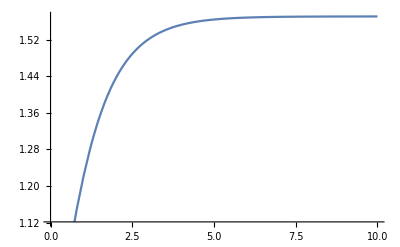

```mathematica
Plot[ArcTan[E^x],{x,0,10}]
```

```mathematica
Integrate[1/chη,η]
Series[%//TrigToExp//PowerExpand,{μ,0,1}]//ExpToTrig
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

-(ⅈ (l Log[-(ⅈ (Cosh[(2 η)/l]-Sinh[(2 η)/l]))/(2 √μ)]-l Log[(ⅈ (Cosh[(2 η)/l]-Sinh[(2 η)/l]))/(2 √μ)]))/(4 √μ)+(l Cosh[(2 η)/l]+l Sinh[(2 η)/l])+1/3 (-l Cosh[(6 η)/l]-l Sinh[(6 η)/l]) μ+O[μ]^(3/2)

```mathematica
Tan[θ ]==Sinh[(2 η)/l+Log[μ]/2]/1
```

Tan[θ]==Sinh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

ArcTan[1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ]

ArcTan[1/2 ⅇ^(-(2 η)/l)]-(2 ⅇ^((6 η)/l) μ)/(1+4 ⅇ^((4 η)/l))+O[μ]^2

```mathematica
shη//TrigToExp
```

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ

```mathematica
ArcTan[x]//TrigToExp
```

1/2 ⅈ Log[1-ⅈ x]-1/2 ⅈ Log[1+ⅈ x]

```mathematica
I/2(Log[Abs[1-I x]]- Log[Abs[1+I x]]) + I/2(I arg[1-I x]-I arg[1+I x])
%==I/2(I arg[1-I x]-I arg[1+I x])
```

1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])+1/2 ⅈ (Log[Abs[1-ⅈ x]]-Log[Abs[1+ⅈ x]])

1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])+1/2 ⅈ (Log[Abs[1-ⅈ x]]-Log[Abs[1+ⅈ x]])==1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])

```mathematica
Integrate[Series[1/chη//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]
Series[Integrate[1/chη,η,Assumptions->{η∈ Reals}]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)

```mathematica
Integrate[1/chη,η,Assumptions->{η∈ Reals}]//TrigToExp//PowerExpand
Series[%,{μ,0,1}]
```

(ⅈ l Log[1-1/2 ⅈ (-ⅇ^(-(2 η)/l)/(√μ)+ⅇ^((2 η)/l) √μ)])/(4 √μ)-(ⅈ l Log[1+1/2 ⅈ (-ⅇ^(-(2 η)/l)/(√μ)+ⅇ^((2 η)/l) √μ)])/(4 √μ)

-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)+ⅇ^((2 η)/l) l-1/3 (ⅇ^((6 η)/l) l) μ+O[μ]^(3/2)

```mathematica
Integrate[1/chη,η]
Series[shη//TrigToExp//PowerExpand,{μ,0,1}]
ArcTan[Normal@%]
Series[%,{μ,0,1}]
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

ArcTan[1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ]

ArcTan[1/2 ⅇ^(-(2 η)/l)]-(2 ⅇ^((6 η)/l) μ)/(1+4 ⅇ^((4 η)/l))+O[μ]^2

```mathematica
Evaluate[-I/2 Log[(x/I-1)/(x/I+1)]/.x->HoldForm[-I Sin[I z]]]//Simplify
-1/2 I Log[(Sin[I z]+1)/(Sin[I z]-1)]
```

-1/2 ⅈ Log[(-ⅈ+-ⅈ Sin[ⅈ z])/(ⅈ+-ⅈ Sin[ⅈ z])]

-1/2 ⅈ Log[(1+ⅈ Sinh[z])/(-1+ⅈ Sinh[z])]

```mathematica
ArcTan[Sin[x]]//TrigToExp
```

1/2 ⅈ Log[1+1/2 (ⅇ^(-ⅈ x)-ⅇ^(ⅈ x))]-1/2 ⅈ Log[1+1/2 (-ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))]

```mathematica
ArcTan[E^x]
```

ArcTan[ⅇ^x]

```mathematica
chη//TrigToExp
```

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ

```mathematica
1/(μ E^(2 η/l)+E^(-2 η/l))
E^(-2 η/l)/(μ+E^(-4 η/l))
Integrate[%,η]
```

1/(ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ)

ⅇ^(-(2 η)/l)/(ⅇ^(-(4 η)/l)+μ)

(l ArcTan[ⅇ^((2 η)/l) √μ])/(2 √μ)

```mathematica
1/N@EulerGamma
```

1.73245

```mathematica
D[ArcTan[shη],η]
%//TrigToExp//FullSimplify
```

-(2 √μ Cosh[(2 η)/l+Log[μ]/2])/(l (1+μ Sinh[(2 η)/l+Log[μ]/2]^2))

-(4 ⅇ^((2 η)/l) (1+ⅇ^((4 η)/l) μ))/(l-2 ⅇ^((4 η)/l) l (-2+μ)+ⅇ^((8 η)/l) l μ^2)

```mathematica
Integrate[1/chη,η]
D[%,η]//Simplify
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

Sech[(2 η)/l+Log[μ]/2]/(√μ)

```mathematica
1/(chη shη^2)+
```

-(l Csch[(2 η)/l+Log[μ]/2] Hypergeometric2F1[-1/2,1,1/2,-Sinh[(2 η)/l+Log[μ]/2]^2])/(2 μ^(3/2))

```mathematica
1/2 Integrate[chη/shη^2,η]
-(*1/2*)Integrate[1/chη,η]
```

-(l Csch[(2 η)/l+Log[μ]/2])/(4 √μ)

-(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

```mathematica
shη
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
Sinh[(2 η)/l+Log[μ]/2]
-shη
```

Sinh[(2 η)/l+Log[μ]/2]

√μ Sinh[(2 η)/l+Log[μ]/2]